## Emergence of inflaton potential from Asymptotically Safe gravity - Calculations

### D-Dimensional flow equations

```mathematica
EQ1d[f_,v_]:=D[v[t,φ],t]-(-d*v[t,φ]+1/2 (d-2) φ D[v[t,φ],φ]+Subscript[c, d] ((d-1) (d^2-d-3)/(d+2))+Subscript[c, d]((d-2) (d+1) (2 D[f[t,φ],t]-(d-2) φ D[f[t,φ],φ])/(4 (d+2) f[t,φ]))+Subscript[c, d] (2 (d^2-4) f[t,φ]+(d-2) (1+D[v[t,φ],φ,φ]) (2 D[f[t,φ],t]-6 f[t,φ]-(d-2) φ D[f[t,φ],φ])+4 (d-1) D[f[t,φ],φ] (2 D[f[t,φ],φ,t]+(d-1) D[f[t,φ],φ]-(d-2) φ D[f[t,φ],φ,φ]))/(2 (d+2) (2 (d-1) D[f[t,φ],φ]^2+(d-2) f[t,φ] (1+D[v[t,φ],φ,φ]))))
EQ2d[f_,v_]:=D[f[t,φ],t]-((2-d) f[t,φ]+1/2 (d-2) φ D[f[t,φ],φ]-Subscript[c, d] (d^6-2 d^5-15 d^4-46 d^3+38 d^2+96 d-24)/(12 (d+2) (d-1) d)-Subscript[c, d] ((d^5-17 d^3-60 d^2+4 d+48) (2 D[f[t,φ],t]-(d-2) φ D[f[t,φ],φ]))/(48 (d-1) d (d+2) f[t,φ])-Subscript[c, d] ((d-2) f[t,φ] D[f[t,φ],φ,φ]+2 D[f[t,φ],φ]^2) ((d-2) (d+2) f[t,φ]^2+(d-1) D[f[t,φ],φ]^2 ((d-2) φ D[f[t,φ],φ]-2 D[f[t,φ],t])+2 (d-1) f[t,φ] D[f[t,φ],φ] ((2-d) φ D[f[t,φ],φ,φ]+(d+2) D[f[t,φ],φ]+2 D[f[t,φ],φ,t]))/((d+2) f[t,φ] (2 (d-1) D[f[t,φ],φ]^2+(d-2) f[t,φ] (D[v[t,φ],φ,φ]+1))^2)+Subscript[c, d] (D[f[t,φ],φ] ((d-2) φ (4 (d-1) D[f[t,φ],φ,φ]+(d-2) (D[v[t,φ],φ,φ]+1))-8 (d-1) D[f[t,φ],φ,t])+2 (d-2) (d f[t,φ] D[v[t,φ],φ,φ]-D[f[t,φ],t] (D[v[t,φ],φ,φ]+1)))/(24 (2 (d-1) D[f[t,φ],φ]^2+(d-2) f[t,φ] (D[v[t,φ],φ,φ]+1))))
```

```mathematica
(*These are the flow equations for the theory with Action Subscript[Γ, k]=∫d^d x√g(-Subscript[F, k][ψ]R+Subscript[V, k][ψ]+Subscript[d, μ] ψd^μ ψ in 4 dimensions, and computing the flow for the dimensionless quantities f=F/k^2, v=V/k^4, at constant field φ=(φ̄)/k)*)
```

### 4-Dimensional Flow Equations

```mathematica
EQ1[f_,v_]:=D[v[t,φ],t]-(-4*v[t,φ]+ φ D[v[t,φ],φ]+1/(16 Pi^2)+(f[t,φ]+3(D[f[t,φ],φ])^2)/(32 Pi^2(3(D[f[t,φ],φ])^2+f[t,φ](1+D[v[t,φ],φ,φ]))))//FullSimplify
EQ2[f_,v_]:=D[f[t,φ],t]-(-2f[t,φ]+ φ D[f[t,φ],φ]+37/(384 Pi^2)+f[t,φ] 1/(96 Pi^2(3(D[f[t,φ],φ])^2+f[t,φ](1+D[v[t,φ],φ,φ]))^2)((f[t,φ]+3(D[f[t,φ],φ])^2)(1-3D[f[t,φ],φ,φ]+3D[v[t,φ],φ,φ])+2f[t,φ](D[v[t,φ],φ,φ])^2))//FullSimplify
```

### Relevant directions and Fixed Point structure (4D)

```mathematica
(* RHS of equations separated *)
```

```mathematica
RHSEQ1[f_,v_]:=(-4*v[t,φ]+ φ D[v[t,φ],φ]+1/(16 Pi^2)+(f[t,φ]+3(D[f[t,φ],φ])^2)/(32 Pi^2(3(D[f[t,φ],φ])^2+f[t,φ](1+D[v[t,φ],φ,φ]))))//FullSimplify
```

```mathematica
RHSEQ2[f_,v_]:=(-2f[t,φ]+ φ D[f[t,φ],φ]+37/(384 Pi^2)+f[t,φ] 1/(96 Pi^2(3(D[f[t,φ],φ])^2+f[t,φ](1+D[v[t,φ],φ,φ]))^2)((f[t,φ]+3(D[f[t,φ],φ])^2)(1-3D[f[t,φ],φ,φ]+3D[v[t,φ],φ,φ])+2f[t,φ](D[v[t,φ],φ,φ])^2))//FullSimplify
```

```mathematica
(*Perturbation around the fixed point, to determine relevant operators*)
```

```mathematica
FPF[t_,φ_]:= 41/(768 π^2);
FPV[t_,φ_]:= 3/(128 π^2);
PertFPF[t_,φ_]:= FPF[t,φ]+ϵ*(δF[φ]+ϵ*δFF[φ] t^α)Exp[λ*t];
PertFPV[t_,φ_]:= FPV[t,φ]+ϵ*(δV[φ]+ϵ*δVV[φ] t^α)Exp[λ*t];
LinPertFPF[t_,φ_]:= FPF[t,φ]+ϵ*(δF[t,φ]);
LinPertFPV[t_,φ_]:= FPV[t,φ]+ϵ*(δV[t,φ]);
```

```mathematica
ExplicitLinPertFPF[t_,φ_]:= FPF[t,φ]+ϵ*(δFP[φ])ⅇ^(λ*t);
ExplicitLinPertFPV[t_,φ_]:= FPV[t,φ]+ϵ*(δVP[φ])ⅇ^(λ*t) ;

ExplicitLinPertFPFquad[t_,φ_]:= FPF[t,φ]+ϵ*(δFP[φ^2])ⅇ^(λ*t);
ExplicitLinPertFPVquad[t_,φ_]:= FPV[t,φ]+ϵ*(δVP[φ^2])ⅇ^(λ*t) ;(*(Hypergeometric1F1[-2-λ/2,1/2,16 π^2 φ^2]) C[2]*)
```

```mathematica
(*Eigendirections equation*)
```

```mathematica
EQ1[ExplicitLinPertFPF,ExplicitLinPertFPV]+O[ϵ,0]^2//FullSimplify
EQ2[ExplicitLinPertFPF,ExplicitLinPertFPV]+O[ϵ,0]^2//FullSimplify
```

1/32 ⅇ^(t λ) (32 (4+λ) δVP[φ]-32 φ δVP'[φ]+δVP''[φ]/π^2) ϵ+O[ϵ]^2

(ⅇ^(t λ) (96 π^2 ((2+λ) δFP[φ]-φ δFP'[φ])+3 δFP''[φ]-δVP''[φ]) ϵ)/(96 π^2)+O[ϵ]^2

```mathematica
(*we restrict the analysis to even functions only*)
```

```mathematica
(EQ1[ExplicitLinPertFPFquad,ExplicitLinPertFPVquad]+O[ϵ,0]^2)/.φ^2->ψ/.φ->Sqrt[ψ]//FullSimplify
(EQ2[ExplicitLinPertFPFquad,ExplicitLinPertFPVquad]+O[ϵ,0]^2)/.φ^2->ψ/.φ->Sqrt[ψ]//FullSimplify
```

(ⅇ^(t λ) (δVP'[ψ]+16 π^2 ((4+λ) δVP[ψ]-2 ψ δVP'[ψ])+2 ψ δVP''[ψ]) ϵ)/(16 π^2)+O[ϵ]^2

(ⅇ^(t λ) (48 π^2 (2+λ) δFP[ψ]+(3-96 π^2 ψ) δFP'[ψ]-δVP'[ψ]+6 ψ δFP''[ψ]-2 ψ δVP''[ψ]) ϵ)/(48 π^2)+O[ϵ]^2

```mathematica
DSolve[{δVP'[ψ]+16 π^2 ((4+λ) δVP[ψ]-2 ψ δVP'[ψ])+2 ψ δVP''[ψ]==0,δVP[0]==0},δVP[ψ],ψ]//FullSimplify
```

DSolve::bvnr: For some branches of the general solution, the given boundary conditions do not restrict the existing freedom in the general solution.

{{δVP[ψ]→√ψ (C[1] HypergeometricU[1/2 (-3-λ),3/2,16 π^2 ψ]+C[2] LaguerreL[(3+λ)/2,1/2,16 π^2 ψ])}}

```mathematica
(*From here one can see that only certain values of lambda are allowed, giving the critical exponents for each of those directions*)
```

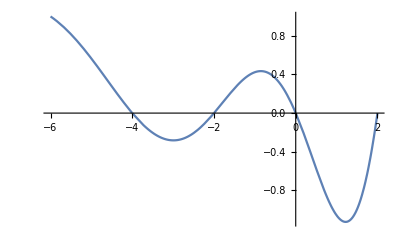

```mathematica
Plot[1/Gamma[-2-λ/2],{λ,-6,2}]
```

```mathematica
(*Making an analysis of the irrelevant directions using a quadratic truncation: *)

MargPertf[t_,φ_]:=af[t]+m1[t] φ^2(*+λ1[t] φ^4*)(*/.ϵ->1/(192 π^2)*);

MargPertv[t_,φ_]:=av[t]+m2[t] φ^2(*+λ2[t] φ^4*)(*/.ϵ->1/(192 π^2)*);
EQ1[MargPertf, MargPertv]+O[φ,0]^3//FullSimplify//Normal
EQ2[MargPertf, MargPertv]+O[φ,0]^3//FullSimplify//Normal
```

4 av[t]-(3+4 m2[t])/(32 π^2 (1+2 m2[t]))+av'[t]+φ^2 (m2[t] (2-(3 m1[t]^2)/(4 af[t] (π+2 π m2[t])^2))+m2'[t])

-37/(384 π^2)+2 af[t]-(1-6 m1[t]+6 m2[t]+8 m2[t]^2)/(96 (π+2 π m2[t])^2)+af'[t]+φ^2 ((m1[t]^2 (6 m1[t] (-1+2 m2[t])+(1+2 m2[t])^2))/(8 π^2 af[t] (1+2 m2[t])^3)+m1'[t])

```mathematica
(*find the beta functions of these truncation*)
```

```mathematica
Solve[{4 av[t]-(3+4 m2[t])/(32 π^2 (1+2 m2[t]))+av'[t]==0,m2[t] (2-(3 m1[t]^2)/(4 af[t] (π+2 π m2[t])^2))+m2'[t]==0-37/(384 π^2)+2 af[t]-(1-6 m1[t]+6 m2[t]+8 m2[t]^2)/(96 (π+2 π m2[t])^2)+af'[t]==0,(m1[t]^2 (6 m1[t] (-1+2 m2[t])+(1+2 m2[t])^2))/(8 π^2 af[t] (1+2 m2[t])^3)+m1'[t]==0},{av'[t],af'[t],m1'[t],m2'[t]}]//FullSimplify
betastruncquad=Values@Solve[{4 av[t]-(3+4 m2[t])/(32 π^2 (1+2 m2[t]))+av'[t]==0,m2[t] (2-(3 m1[t]^2)/(4 af[t] (π+2 π m2[t])^2))+m2'[t]==0-37/(384 π^2)+2 af[t]-(1-6 m1[t]+6 m2[t]+8 m2[t]^2)/(96 (π+2 π m2[t])^2)+af'[t]==0,(m1[t]^2 (6 m1[t] (-1+2 m2[t])+(1+2 m2[t])^2))/(8 π^2 af[t] (1+2 m2[t])^3)+m1'[t]==0},{av'[t],af'[t],m1'[t],m2'[t]}][[1]]//FullSimplify
```

{{av'[t]→-4 av[t]+(3+4 m2[t])/(32 π^2 (1+2 m2[t])),af'[t]→-2 af[t]+(-24 m1[t]+(1+2 m2[t]) (41+90 m2[t]))/(384 (π+2 π m2[t])^2),m1'[t]→-(m1[t]^2 (6 m1[t] (-1+2 m2[t])+(1+2 m2[t])^2))/(8 π^2 af[t] (1+2 m2[t])^3),m2'[t]→1/4 m2[t] (-8+(3 m1[t]^2)/(af[t] (π+2 π m2[t])^2))}}

{-4 av[t]+(3+4 m2[t])/(32 π^2 (1+2 m2[t])),-2 af[t]+(-24 m1[t]+(1+2 m2[t]) (41+90 m2[t]))/(384 (π+2 π m2[t])^2),-(m1[t]^2 (6 m1[t] (-1+2 m2[t])+(1+2 m2[t])^2))/(8 π^2 af[t] (1+2 m2[t])^3),1/4 m2[t] (-8+(3 m1[t]^2)/(af[t] (π+2 π m2[t])^2))}

```mathematica
(*Fixed point of this truncation*)
```

```mathematica
betastruncquad/.m1[t]->0/.m2[t]->0/.af[t]->41/(768 π^2)/.av[t]->3/(128 π^2)
```

{0,0,0,0}

```mathematica
(*Critical Exponents of the gravitational sector*)
```

```mathematica
Eigenvalues[({D[betastruncquad[[;;2]],av[t]],D[betastruncquad[[;;2]],af[t]]}/.m1[t]->0/.m2[t]->0/.af[t]->41/(768 π^2)/.av[t]->3/(128 π^2))]
Eigenvectors[({D[betastruncquad[[;;2]],av[t]],D[betastruncquad[[;;2]],af[t]]}/.m1[t]->0/.m2[t]->0/.af[t]->41/(768 π^2)/.av[t]->3/(128 π^2))]
```

{-4,-2}

{{1,0},{0,1}}

```mathematica
(*Perturbation of the beta functions on the suposedely marginal direction*)
```

```mathematica
(betastruncquad/.m1[t]->ϵ*α 32 π^2 δm1[t]/.m2[t]->0/.af[t]->41/(768 π^2)+β*ϵ*δaf[t]/.av[t]->3/(128 π^2))
```

{0,-2 (41/(768 π^2)+β ϵ δaf[t])+(41-768 π^2 α ϵ δm1[t])/(384 π^2),-(128 π^2 α^2 ϵ^2 δm1[t]^2 (1-192 π^2 α ϵ δm1[t]))/(41/(768 π^2)+β ϵ δaf[t]),0}

```mathematica
(*Flow equations of such perturbations*)
```

```mathematica
{D[β*δaf[t],t]==-2 (41/(768 π^2)+β δaf[t])+(41-768 π^2 α  δm1[t])/(384 π^2),D[α 32 π^2 δm1[t],t]==-(128 π^2 α^2  δm1[t]^2 (1-192 π^2 α δm1[t]))/(41/(768 π^2)+β δaf[t])}/.β->-1/.α->1//FullSimplify
```

{2 δaf[t]+δaf'[t]==2 δm1[t],(3072 π^2 δm1[t]^2 (-1+192 π^2 δm1[t]))/(-41+768 π^2 δaf[t])+δm1'[t]==0}

```mathematica
(*solution for one of the perturbations*)
```

```mathematica
DSolve[(3072 π^2 δm1[k]^2 (-1))/41==k*D[δm1[k],k],δm1[k],k]/.C[1]->3072/41 π^2 (Log[k]-Log[k/k0])//FullSimplify
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{{δm1[k]→41/(3072 π^2 Log[k/k0])}}

```mathematica
(*Solution for the other perturbation*)
```

```mathematica
DSolve[k D[β*δaf[k],k]==-2 (β δaf[k]+ 41/(3072 π^2 Log[k/k0])),δaf[k],k]//FullSimplify
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{{δaf[k]→C[1]/k^2-(41 k0^2 ExpIntegralEi[2 Log[k/k0]])/(1536 k^2 π^2 β)}}

### Numerical solution Flow Equations (4D)

#### Construction of the flow equations in the convenient variables

```mathematica
(*We change to a dimensionless variable in order to use numerical methods*)
```

```mathematica
TransformationToConstantPhi=Join[Join[Table[D[f[t,φ],{φ,n}]->(G[t])^n D[f[t,ϕ],{ϕ,n}],{n,0,4}],Table[D[f[t,φ],{φ,n},t]->(G[t])^n(n*D[G[t],t]/G[t] D[f[t,ϕ],{ϕ,n}]+D[f[t,ϕ],{ϕ,n},t]+D[G[t],t]/G[t] ϕ*D[f[t,ϕ],{ϕ,n+1}]),{n,0,4}]],Join[Table[D[v[t,φ],{φ,n}]->(G[t])^n D[v[t,ϕ],{ϕ,n}],{n,0,4}],Table[D[v[t,φ],{φ,n},t]->(G[t])^n(n*D[G[t],t]/G[t] D[v[t,ϕ],{ϕ,n}]+D[v[t,ϕ],{ϕ,n},t]+D[G[t],t]/G[t] ϕ*D[v[t,ϕ],{ϕ,n+1}]),{n,0,4}]]]//Expand;
φToConstantPhi={φ->ϕ/G[t]};
```

```mathematica
(EQ1[f,v]/.TransformationToConstantPhi)/.φToConstantPhi//FullSimplify
(EQ2[f,v]/.TransformationToConstantPhi)/.φToConstantPhi//FullSimplify
```

4 v[t,ϕ]+ϕ (-1+G'[t]/G[t]) v^(0,1)[t,ϕ]-(2+(f[t,ϕ]+3 G[t]^2 (f^(0,1)[t,ϕ])^2)/(f[t,ϕ]+3 G[t]^2 (f^(0,1)[t,ϕ])^2+f[t,ϕ] G[t]^2 v^(0,2)[t,ϕ]))/(32 π^2)+v^(1,0)[t,ϕ]

-37/(384 π^2)+2 f[t,ϕ]-ϕ f^(0,1)[t,ϕ]+(ϕ G'[t] f^(0,1)[t,ϕ])/G[t]-(f[t,ϕ] (2 f[t,ϕ] G[t]^4 (v^(0,2)[t,ϕ])^2+(f[t,ϕ]+3 G[t]^2 (f^(0,1)[t,ϕ])^2) (1+3 G[t]^2 (-f^(0,2)[t,ϕ]+v^(0,2)[t,ϕ]))))/(96 π^2 (3 G[t]^2 (f^(0,1)[t,ϕ])^2+f[t,ϕ] (1+G[t]^2 v^(0,2)[t,ϕ]))^2)+f^(1,0)[t,ϕ]

```mathematica
EqReplacedConstantPhiv[f_,v_]:=4 v[t,ϕ]+ϕ (-1+G'[t]/G[t]) Derivative[0,1][v][t,ϕ]-(2+(f[t,ϕ]+3 G[t]^2 (Derivative[0,1][f][t,ϕ])^2)/(f[t,ϕ]+3 G[t]^2 (Derivative[0,1][f][t,ϕ])^2+f[t,ϕ] G[t]^2 Derivative[0,2][v][t,ϕ]))/(32 π^2)+Derivative[1,0][v][t,ϕ]
EqReplacedConstantPhif[f_,v_]:=-37/(384 π^2)+2 f[t,ϕ]-ϕ Derivative[0,1][f][t,ϕ]+(ϕ G'[t] Derivative[0,1][f][t,ϕ])/G[t]-(f[t,ϕ] (2 f[t,ϕ] G[t]^4 (Derivative[0,2][v][t,ϕ])^2+(f[t,ϕ]+3 G[t]^2 (Derivative[0,1][f][t,ϕ])^2) (1+3 G[t]^2 (-Derivative[0,2][f][t,ϕ]+Derivative[0,2][v][t,ϕ]))))/(96 π^2 (3 G[t]^2 (Derivative[0,1][f][t,ϕ])^2+f[t,ϕ] (1+G[t]^2 Derivative[0,2][v][t,ϕ]))^2)+Derivative[1,0][f][t,ϕ]
```

```mathematica
(*we split the potentials, and use the change of variables, to parameterize the k dependence using the coupling G *)
```

```mathematica
Fluctf[t_,φ_]:=1/(16 Pi (G[t])^2)+f[G[t],φ^2]/(16 Pi (G[t])^2);
Fluctv[t_,φ_]:=(2Λ[t])/(16 Pi (G[t])^2)+v[G[t],φ^2]/((16 Pi (G[t])^2)^2);
```

```mathematica
PerturbedRFP1=EqReplacedConstantPhiv[Fluctf,Fluctv]//FullSimplify
PerturbedRFP2=EqReplacedConstantPhif[Fluctf,Fluctv]//FullSimplify
```

1/(256 π^2)((4 (v[G[t],ϕ^2]+32 π G[t]^2 Λ[t]))/G[t]^4-(4 v[G[t],ϕ^2] G'[t])/G[t]^5-(64 π Λ[t] G'[t])/G[t]^3+(32 π Λ'[t])/G[t]^2+(2 ϕ^2 (-G[t]+G'[t]) v^(0,1)[G[t],ϕ^2])/G[t]^5-(16 (48 π G[t]^2 (4 π (1+f[G[t],ϕ^2])+3 ϕ^2 (f^(0,1)[G[t],ϕ^2])^2)+(1+f[G[t],ϕ^2]) (v^(0,1)[G[t],ϕ^2]+2 ϕ^2 v^(0,2)[G[t],ϕ^2])))/(32 π G[t]^2 (4 π (1+f[G[t],ϕ^2])+3 ϕ^2 (f^(0,1)[G[t],ϕ^2])^2)+(1+f[G[t],ϕ^2]) (v^(0,1)[G[t],ϕ^2]+2 ϕ^2 v^(0,2)[G[t],ϕ^2]))+(G'[t] v^(1,0)[G[t],ϕ^2])/G[t]^4)

-1/(384 π^2)(37-(48 π (1+f[G[t],ϕ^2]))/G[t]^2+(48 π G'[t])/G[t]^3+(48 π f[G[t],ϕ^2] G'[t])/G[t]^3+(48 π ϕ^2 f^(0,1)[G[t],ϕ^2])/G[t]^2-(48 π ϕ^2 G'[t] f^(0,1)[G[t],ϕ^2])/G[t]^3+(8 (1+f[G[t],ϕ^2]) (256 π^2 G[t]^4 (4 π (1+f[G[t],ϕ^2])+3 ϕ^2 (f^(0,1)[G[t],ϕ^2])^2) (8 π-3 f^(0,1)[G[t],ϕ^2]-6 ϕ^2 f^(0,2)[G[t],ϕ^2])+48 π G[t]^2 (4 π (1+f[G[t],ϕ^2])+3 ϕ^2 (f^(0,1)[G[t],ϕ^2])^2) (v^(0,1)[G[t],ϕ^2]+2 ϕ^2 v^(0,2)[G[t],ϕ^2])+(1+f[G[t],ϕ^2]) (v^(0,1)[G[t],ϕ^2]+2 ϕ^2 v^(0,2)[G[t],ϕ^2])^2))/(32 π G[t]^2 (4 π (1+f[G[t],ϕ^2])+3 ϕ^2 (f^(0,1)[G[t],ϕ^2])^2)+(1+f[G[t],ϕ^2]) (v^(0,1)[G[t],ϕ^2]+2 ϕ^2 v^(0,2)[G[t],ϕ^2]))^2-(24 π G'[t] f^(1,0)[G[t],ϕ^2])/G[t]^2)

```mathematica
(*Replacement of the beta functions of lambda and G, obtained evaluating the two equations at φ=0*)
```

```mathematica
BetasLANDG=Solve[{(PerturbedRFP1/.ϕ->0)==0,(PerturbedRFP2/.ϕ->0)==0},{G'[t],Λ'[t]}][[1]]/.f[G[t],0]->0/.v[G[t],0]->0//FullSimplify
```

{G'[t]→(-8192 π^3 G[t]^5 (96 π^2+G[t]^2 (-82 π+3 f^(0,1)[G[t],0]))-256 π^2 G[t]^3 (48 π-43 G[t]^2) v^(0,1)[G[t],0]+3 G[t] (-16 π+15 G[t]^2) (v^(0,1)[G[t],0])^2)/(24 π (128 π^2 G[t]^2+v^(0,1)[G[t],0])^2 (-2+G[t] f^(1,0)[G[t],0])),Λ'[t]→(64 π G[t] (8192 π^3 G[t]^6 (-36 π+Λ[t] (82 π-3 f^(0,1)[G[t],0]))+48 π Λ[t] (v^(0,1)[G[t],0])^2+3 G[t]^2 v^(0,1)[G[t],0] (4096 π^3 Λ[t]+(-4+15 Λ[t]) v^(0,1)[G[t],0])+256 π^2 G[t]^4 (3072 π^3 Λ[t]+(-15+43 Λ[t]) v^(0,1)[G[t],0])+147456 π^4 G[t]^7 f^(1,0)[G[t],0]-48 π G[t] Λ[t] (v^(0,1)[G[t],0])^2 f^(1,0)[G[t],0]+6 G[t]^3 v^(0,1)[G[t],0] (-2048 π^3 Λ[t]+v^(0,1)[G[t],0]) f^(1,0)[G[t],0]+384 π^2 G[t]^5 (-2048 π^3 Λ[t]+5 v^(0,1)[G[t],0]) f^(1,0)[G[t],0])+(8192 π^3 G[t]^4 (96 π^2+G[t]^2 (-82 π+3 f^(0,1)[G[t],0]))+256 π^2 G[t]^2 (48 π-43 G[t]^2) v^(0,1)[G[t],0]+3 (16 π-15 G[t]^2) (v^(0,1)[G[t],0])^2) v^(1,0)[G[t],0])/(768 π^2 G[t] (128 π^2 G[t]^2+v^(0,1)[G[t],0])^2 (-2+G[t] f^(1,0)[G[t],0]))}

```mathematica
(*Replacement to more convenient variables, where I only use the square of the field as a variable*)
```

```mathematica
((((PerturbedRFP1/.ϕ^2 ->ψ/.ϕ^4 ->(ψ)^2)-(PerturbedRFP1/.ϕ^2 ->ψ/.ϕ^4 ->(ψ)^2/.ψ->0/.f[G[t],0]->0/.v[G[t],0]->0/.Derivative[1,0][v][G[t],0]->0/.Derivative[1,0][f][G[t],0]->0))//FullSimplify//Expand//FullSimplify)/.BetasLANDG/.G[t]->G/.Λ[t]->Λ/.f[G[t],0]->0/.v[G[t],0]->0/.Derivative[1,0][v][G[t],0]->0/.Derivative[1,0][f][G[t],0]->0)//FullSimplify
((PerturbedRFP2/.BetasLANDG/.G[t]->G/.Λ[t]->Λ/.ϕ^2 ->ψ/.ϕ^4 ->(ψ)^2/.f[G[t],0]->0/.v[G[t],0]->0/.Derivative[1,0][v][G[t],0]->0/.Derivative[1,0][f][G[t],0]->0)//FullSimplify)
```

1/(256 G^5 π^2)((256 G^7 π (-((4 π (1+f[G,ψ])+3 ψ (f^(0,1)[G,ψ])^2) v^(0,1)[G,0])+4 π (1+f[G,ψ]) (v^(0,1)[G,ψ]+2 ψ v^(0,2)[G,ψ])))/((128 G^2 π^2+v^(0,1)[G,0]) (32 G^2 π (4 π (1+f[G,ψ])+3 ψ (f^(0,1)[G,ψ])^2)+(1+f[G,ψ]) (v^(0,1)[G,ψ]+2 ψ v^(0,2)[G,ψ])))+((24576 G^7 π^3 f^(0,1)[G,0]-G (128 G^2 π^2+v^(0,1)[G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) v^(0,1)[G,0])) (2 v[G,ψ]-ψ v^(0,1)[G,ψ]))/(12 π (128 G^2 π^2+v^(0,1)[G,0])^2 (-2+G f^(1,0)[G,0]))+G (4 v[G,ψ]-2 ψ v^(0,1)[G,ψ]+(G (-24576 G^6 π^3 f^(0,1)[G,0]+(128 G^2 π^2+v^(0,1)[G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) v^(0,1)[G,0])) v^(1,0)[G,ψ])/(24 π (128 G^2 π^2+v^(0,1)[G,0])^2 (-2+G f^(1,0)[G,0]))))

-1/(384 π^2)(37-(48 π (1+f[G,ψ]))/G^2+(48 π ψ f^(0,1)[G,ψ])/G^2+(8 (1+f[G,ψ]) (256 G^4 π^2 (4 π (1+f[G,ψ])+3 ψ (f^(0,1)[G,ψ])^2) (8 π-3 f^(0,1)[G,ψ]-6 ψ f^(0,2)[G,ψ])+48 G^2 π (4 π (1+f[G,ψ])+3 ψ (f^(0,1)[G,ψ])^2) (v^(0,1)[G,ψ]+2 ψ v^(0,2)[G,ψ])+(1+f[G,ψ]) (v^(0,1)[G,ψ]+2 ψ v^(0,2)[G,ψ])^2))/(32 G^2 π (4 π (1+f[G,ψ])+3 ψ (f^(0,1)[G,ψ])^2)+(1+f[G,ψ]) (v^(0,1)[G,ψ]+2 ψ v^(0,2)[G,ψ]))^2+(2 ψ f^(0,1)[G,ψ] (24576 G^6 π^3 f^(0,1)[G,0]-(128 G^2 π^2+v^(0,1)[G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) v^(0,1)[G,0])))/(G^2 (128 G^2 π^2+v^(0,1)[G,0])^2 (-2+G f^(1,0)[G,0]))+(2 f[G,ψ] (-24576 G^6 π^3 f^(0,1)[G,0]+(128 G^2 π^2+v^(0,1)[G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) v^(0,1)[G,0])))/(G^2 (128 G^2 π^2+v^(0,1)[G,0])^2 (-2+G f^(1,0)[G,0]))+(-49152 G^6 π^3 f^(0,1)[G,0]+2 (128 G^2 π^2+v^(0,1)[G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) v^(0,1)[G,0]))/(G^2 (128 G^2 π^2+v^(0,1)[G,0])^2 (-2+G f^(1,0)[G,0]))+((24576 G^6 π^3 f^(0,1)[G,0]-(128 G^2 π^2+v^(0,1)[G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) v^(0,1)[G,0])) f^(1,0)[G,ψ])/(G (128 G^2 π^2+v^(0,1)[G,0])^2 (-2+G f^(1,0)[G,0])))

```mathematica
(*Definition of the resultign equations, with the beta functions of the gravitational sector already replaced, the dimensionless variables also replaced, thereplacement of the splitting f the interactions, and all simplifications performed. This are the final equations that we will use to find a numerical solution*)
```

```mathematica
PerturbedRFP1Func[f_,v_]:=1/(256 G^5 π^2)((256 G^7 π (-((4 π (1+f[G,ψ])+3 ψ (Derivative[0,1][f][G,ψ])^2) Derivative[0,1][v][G,0])+4 π (1+f[G,ψ]) (Derivative[0,1][v][G,ψ]+2 ψ Derivative[0,2][v][G,ψ])))/((128 G^2 π^2+Derivative[0,1][v][G,0]) (32 G^2 π (4 π (1+f[G,ψ])+3 ψ (Derivative[0,1][f][G,ψ])^2)+(1+f[G,ψ]) (Derivative[0,1][v][G,ψ]+2 ψ Derivative[0,2][v][G,ψ])))+((24576 G^7 π^3 Derivative[0,1][f][G,0]-G (128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0])) (2 v[G,ψ]-ψ Derivative[0,1][v][G,ψ]))/(12 π (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0]))+G (4 v[G,ψ]-2 ψ Derivative[0,1][v][G,ψ]+(G (-24576 G^6 π^3 Derivative[0,1][f][G,0]+(128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0])) Derivative[1,0][v][G,ψ])/(24 π (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0]))));
PerturbedRFP2Func[f_,v_]:=-1/(384 π^2)(37-(48 π (1+f[G,ψ]))/G^2+(48 π ψ Derivative[0,1][f][G,ψ])/G^2+(8 (1+f[G,ψ]) (256 G^4 π^2 (4 π (1+f[G,ψ])+3 ψ (Derivative[0,1][f][G,ψ])^2) (8 π-3 Derivative[0,1][f][G,ψ]-6 ψ Derivative[0,2][f][G,ψ])+48 G^2 π (4 π (1+f[G,ψ])+3 ψ (Derivative[0,1][f][G,ψ])^2) (Derivative[0,1][v][G,ψ]+2 ψ Derivative[0,2][v][G,ψ])+(1+f[G,ψ]) (Derivative[0,1][v][G,ψ]+2 ψ Derivative[0,2][v][G,ψ])^2))/(32 G^2 π (4 π (1+f[G,ψ])+3 ψ (Derivative[0,1][f][G,ψ])^2)+(1+f[G,ψ]) (Derivative[0,1][v][G,ψ]+2 ψ Derivative[0,2][v][G,ψ]))^2+(2 ψ Derivative[0,1][f][G,ψ] (24576 G^6 π^3 Derivative[0,1][f][G,0]-(128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0])))/(G^2 (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0]))+(2 f[G,ψ] (-24576 G^6 π^3 Derivative[0,1][f][G,0]+(128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0])))/(G^2 (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0]))+(-49152 G^6 π^3 Derivative[0,1][f][G,0]+2 (128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0]))/(G^2 (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0]))+((24576 G^6 π^3 Derivative[0,1][f][G,0]-(128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0])) Derivative[1,0][f][G,ψ])/(G (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0])));
```

```mathematica
(*Just a check of the fixed point in this parameterization. now k -> Infinity is G->Sqrt[48 π/41]*)
```

```mathematica
PerturbedRFP1Func[f,v]/.G->Sqrt[48 π/41]/.f[Sqrt[48 π/41],ψ]->0/.v[Sqrt[48 π/41],ψ]->0/. Derivative[0,1][v][4 √((3 π)/41),ψ]->0/. Derivative[0,1][f][4 √((3 π)/41),ψ]->0/. Derivative[0,1][v][4 √((3 π)/41),0]->0/. Derivative[0,1][f][4 √((3 π)/41),0]->0/.Derivative[0,2][f][4 √((3 π)/41),ψ]->0/.Derivative[0,2][v][4 √((3 π)/41),ψ]->0//Simplify
PerturbedRFP2Func[f,v]/.G->Sqrt[48 π/41]/.f[Sqrt[48 π/41],ψ]->0/.v[Sqrt[48 π/41],ψ]->0/. Derivative[0,1][v][4 √((3 π)/41),ψ]->0/. Derivative[0,1][f][4 √((3 π)/41),ψ]->0/. Derivative[0,1][v][4 √((3 π)/41),0]->0/. Derivative[0,1][f][4 √((3 π)/41),0]->0/.Derivative[0,2][f][4 √((3 π)/41),ψ]->0/.Derivative[0,2][v][4 √((3 π)/41),ψ]->0//Simplify
```

0

0

#### Boundary conditions for the two unknown potentials

```mathematica
(*To find the boundary conditions, we solve the flow equations near vanishing field*)
```

```mathematica
Linearizedf[G_,ψ_]:=ϵ*f[G,ψ];
Linearizedv[G_,ψ_]:=ϵ*v[G,ψ];
```

```mathematica
(*We have to expand each equation up to the lowest non trivia order. In the case of v is up to first order, in the case of F one has to go one order higher to get a non trivial solution*)
```

```mathematica
((PerturbedRFP1Func[Linearizedf,Linearizedv]+O[ϵ,0]^2//Normal)/.ϵ->1//Simplify)/.Derivative[0,1][f][G,0]->F1[G]/.Derivative[0,1][v][G,0]->V1[G]//Simplify
((PerturbedRFP2Func[Linearizedf,Linearizedv]+O[ϵ,0]^3)//Simplify)/.Derivative[0,1][f][G,0]->F1[G]/.Derivative[0,1][v][G,0]->V1[G]//Simplify
```

(164 G π v[G,ψ]-3 G V1[G]+3 G v^(0,1)[G,ψ]-82 G π ψ v^(0,1)[G,ψ]+6 G ψ v^(0,2)[G,ψ]-41 G^2 π v^(1,0)[G,ψ]+48 π^2 v^(1,0)[G,ψ])/(12288 G^3 π^4)

1/(12288 G^2 π^4)(1312 G^2 π^2 f[G,ψ]-48 G^2 π F1[G]+V1[G]+48 G^2 π f^(0,1)[G,ψ]-1312 G^2 π^2 ψ f^(0,1)[G,ψ]-v^(0,1)[G,ψ]+96 G^2 π ψ f^(0,2)[G,ψ]-2 ψ v^(0,2)[G,ψ]+656 G^3 π^2 f^(1,0)[G,0]-768 G π^3 f^(1,0)[G,0]-656 G^3 π^2 f^(1,0)[G,ψ]+768 G π^3 f^(1,0)[G,ψ]) ϵ-1/(1572864 (G^4 π^6))(V1[G]^2+128 G^2 π^2 ψ V1[G] f^(0,1)[G,ψ]-12288 G^4 π^3 ψ (f^(0,1)[G,ψ])^2+96 G^2 π f^(0,1)[G,ψ] v^(0,1)[G,ψ]-(v^(0,1)[G,ψ])^2+192 G^2 π ψ v^(0,1)[G,ψ] f^(0,2)[G,ψ]+192 G^2 π ψ f^(0,1)[G,ψ] v^(0,2)[G,ψ]-4 ψ v^(0,1)[G,ψ] v^(0,2)[G,ψ]+384 G^2 π ψ^2 f^(0,2)[G,ψ] v^(0,2)[G,ψ]-4 ψ^2 (v^(0,2)[G,ψ])^2-64 G^3 π^2 V1[G] f^(1,0)[G,0]+83968 G^5 π^4 ψ f^(0,1)[G,ψ] f^(1,0)[G,0]-98304 G^3 π^5 ψ f^(0,1)[G,ψ] f^(1,0)[G,0]-41984 G^6 π^4 (f^(1,0)[G,0])^2+49152 G^4 π^5 (f^(1,0)[G,0])^2-128 G^2 π^2 f[G,ψ] (-48 G^2 π F1[G]+V1[G]+16 G (41 G^2-48 π) π^2 f^(1,0)[G,0])+96 F1[G] (-G^2 π V1[G]+32 G^4 π^3 (-2 ψ f^(0,1)[G,ψ]+G (f^(1,0)[G,0]-f^(1,0)[G,ψ])))+64 G^3 π^2 V1[G] f^(1,0)[G,ψ]+41984 G^6 π^4 f^(1,0)[G,0] f^(1,0)[G,ψ]-49152 G^4 π^5 f^(1,0)[G,0] f^(1,0)[G,ψ]) ϵ^2+O[ϵ]^3

```mathematica
(164 G π v[G,ψ]-3 G V1[G]+3 G Derivative[0,1][v][G,ψ]-82 G π ψ Derivative[0,1][v][G,ψ]+6 G ψ Derivative[0,2][v][G,ψ]-41 G^2 π Derivative[1,0][v][G,ψ]+48 π^2 Derivative[1,0][v][G,ψ])/(12288 G^3 π^4)/.f[G,ψ]->F1[G]ψ/.D[f[G,ψ]->F1[G]ψ,ψ]/.D[f[G,ψ]->F1[G]ψ,ψ,ψ]/.D[f[G,ψ]->F1[G]ψ,G]/.D[f[G,ψ]->F1[G]ψ,ψ,G]/.v[G,ψ]->V1[G]ψ/.D[v[G,ψ]->V1[G]ψ,ψ]/.D[v[G,ψ]->V1[G]ψ,ψ,ψ]/.D[v[G,ψ]->V1[G]ψ,G]/.D[v[G,ψ]->V1[G]ψ,ψ,G]/.Derivative[1,0][f][G,0]->0/.Derivative[1,0][v][G,0]->0//FullSimplify
```

(ψ (82 G V1[G]+(-41 G^2+48 π) V1'[G]))/(12288 G^3 π^3)

```mathematica
(*V is easy to solve, so we can find the boundary condition for these potential being*)
```

```mathematica
DSolve[82 G V1[G]+(-41 G^2+48 π) V1'[G]==0,V1[G],G]
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{{V1[G]→(41 G^2-48 π) C[1]}}

```mathematica
1/(12288 G^2 π^4)(1312 G^2 π^2 f[G,ψ]-48 G^2 π F1[G]+V1[G]+48 G^2 π Derivative[0,1][f][G,ψ]-1312 G^2 π^2 ψ Derivative[0,1][f][G,ψ]-Derivative[0,1][v][G,ψ]+96 G^2 π ψ Derivative[0,2][f][G,ψ]-2 ψ Derivative[0,2][v][G,ψ]+656 G^3 π^2 Derivative[1,0][f][G,0]-768 G π^3 Derivative[1,0][f][G,0]-656 G^3 π^2 Derivative[1,0][f][G,ψ]+768 G π^3 Derivative[1,0][f][G,ψ]) -1/(1572864 (G^4 π^6))(V1[G]^2+128 G^2 π^2 ψ V1[G] Derivative[0,1][f][G,ψ]-12288 G^4 π^3 ψ (Derivative[0,1][f][G,ψ])^2+96 G^2 π Derivative[0,1][f][G,ψ] Derivative[0,1][v][G,ψ]-(Derivative[0,1][v][G,ψ])^2+192 G^2 π ψ Derivative[0,1][v][G,ψ] Derivative[0,2][f][G,ψ]+192 G^2 π ψ Derivative[0,1][f][G,ψ] Derivative[0,2][v][G,ψ]-4 ψ Derivative[0,1][v][G,ψ] Derivative[0,2][v][G,ψ]+384 G^2 π ψ^2 Derivative[0,2][f][G,ψ] Derivative[0,2][v][G,ψ]-4 ψ^2 (Derivative[0,2][v][G,ψ])^2-64 G^3 π^2 V1[G] Derivative[1,0][f][G,0]+83968 G^5 π^4 ψ Derivative[0,1][f][G,ψ] Derivative[1,0][f][G,0]-98304 G^3 π^5 ψ Derivative[0,1][f][G,ψ] Derivative[1,0][f][G,0]-41984 G^6 π^4 (Derivative[1,0][f][G,0])^2+49152 G^4 π^5 (Derivative[1,0][f][G,0])^2-128 G^2 π^2 f[G,ψ] (-48 G^2 π F1[G]+V1[G]+16 G (41 G^2-48 π) π^2 Derivative[1,0][f][G,0])+96 F1[G] (-G^2 π V1[G]+32 G^4 π^3 (-2 ψ Derivative[0,1][f][G,ψ]+G (Derivative[1,0][f][G,0]-Derivative[1,0][f][G,ψ])))+64 G^3 π^2 V1[G] Derivative[1,0][f][G,ψ]+41984 G^6 π^4 Derivative[1,0][f][G,0] Derivative[1,0][f][G,ψ]-49152 G^4 π^5 Derivative[1,0][f][G,0] Derivative[1,0][f][G,ψ]) /.f[G,ψ]->F1[G]ψ/.D[f[G,ψ]->F1[G]ψ,ψ]/.D[f[G,ψ]->F1[G]ψ,ψ,ψ]/.D[f[G,ψ]->F1[G]ψ,G]/.D[f[G,ψ]->F1[G]ψ,ψ,G]/.v[G,ψ]->V1[G]ψ/.D[v[G,ψ]->V1[G]ψ,ψ]/.D[v[G,ψ]->V1[G]ψ,ψ,ψ]/.D[v[G,ψ]->V1[G]ψ,G]/.D[v[G,ψ]->V1[G]ψ,ψ,G]/.Derivative[1,0][f][G,0]->0/.Derivative[1,0][v][G,0]->0//FullSimplify
```

(192 G π ψ F1[G]^2-ψ (-16 π (-82 G^2 π+96 π^2+3 G^2 F1[G])+V1[G]) F1'[G])/(24576 G π^4)

```mathematica
192 G π F1[G]^2- (-16 π (-82 G^2 π+96 π^2+3 G^2 F1[G])+V1[G]) F1'[G]/.V1[G]->V00(48 π-41 G^2)/(48 π)//FullSimplify
```

192 G π F1[G]^2+((-41 G^2+48 π) (1536 π^3-V00) F1'[G])/(48 π)+48 G^2 π F1[G] F1'[G]

```mathematica
(*To get an approximated analytical solution, we neglect the last term, and find*)
```

```mathematica
DSolve[192 G π F1[G]^2+((-41 G^2+48 π) (1536 π^3-V00) F1'[G])/(48 π)==0,F1[G],G]
```

{{F1[G]→-(41 (1536 π^3-V00))/(62976 π^3 C[1]-41 V00 C[1]+4608 π^2 Log[41 G^2-48 π])}}

```mathematica
(*Lowest Non-trivial order also expanded in V, where we are assuming now F>>V, and get the simplest ansatz for a boundary condition of f*)
```

```mathematica
DSolve[12 G  (Subscript[f, 1][G])^2+ (-82 G^2 π+96 π^2) Subscript[f, 1]'[G]==0,Subscript[f, 1][G],G]
```

{{f_1[G]→-(41 π)/(41 π C[1]+3 Log[-41 G^2+48 π])}}

```mathematica
(*Sumarizing boundary conditions here*)
```

```mathematica
LinearizedSolutionsfandv={(41 F00 π)/(41 π-3 F00 Log[((48 π)/41 -G^2)/((48 π)/41)]),V00(((48 π)/41 -G^2)/((48 π)/41))};
```

```mathematica
(*Just a numerical check up of the solutions found, and how well they work given the approximation we made*)
```

{{f_1→InterpolatingFunction[…],v_1→InterpolatingFunction[…]}}

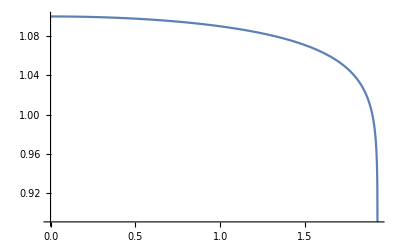

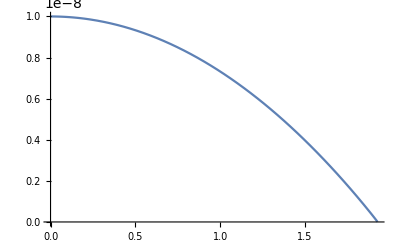

{1.1}

{1.×10^-8}

{0.891053}

{3.12523×10^-12}

```mathematica
Rhof=1000000000;
Rhov=100;

f0=1.1;
v0=1/100000000;
delta=+0.00998;
Ginit=0;
Gfin=√((48 π)/41)+delta;
Solsfvtruncated=NDSolve[{(4096 G^5 π^2 (328 π^2-3 Subscript[f, 1][G] (4 π+3 Subscript[f, 1][G])) Subscript[v, 1][G]+22016 G^3 π^2 (Subscript[v, 1][G])^2+90 G (Subscript[v, 1][G])^3+(24576 G^6 π^3 Subscript[f, 1][G]-(128 G^2 π^2+Subscript[v, 1][G]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Subscript[v, 1][G])) Subscript[v, 1]'[G])==0,((768 G^3 π (Subscript[f, 1][G])^2 (48 G^2 π Subscript[f, 1][G] +(128 G^2 π^2+Subscript[v, 1][G]))+(24576 G^6 π^3 Subscript[f, 1][G]-(128 G^2 π^2+Subscript[v, 1][G]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Subscript[v, 1][G])) Subscript[f, 1]'[G]))==0(*,Subscript[f, 1][Gfin]==Rhof*delta,Subscript[v, 1][Gfin]==Rhov*delta*),Subscript[f, 1][Ginit]==f0,Subscript[v, 1][Ginit]==v0},{Subscript[f, 1],Subscript[v, 1]},{G,Ginit,Gfin}(*,Method->"StiffnessSwitching"*)(*,Method->"Shooting"*),PrecisionGoal->15]
Plot[Evaluate[(Subscript[f, 1][G]/.Solsfvtruncated)/.G->x],{x,Ginit,Gfin},PlotRange->All]
Plot[Evaluate[(Subscript[v, 1][G]/.Solsfvtruncated)/.G->x],{x,Ginit,Gfin},PlotRange->All]
Evaluate[(Subscript[f, 1][G]/.Solsfvtruncated)/.G->Ginit]
Evaluate[(Subscript[v, 1][G]/.Solsfvtruncated)/.G->Ginit]
Evaluate[(Subscript[f, 1][G]/.Solsfvtruncated)/.G->Gfin]
Evaluate[(Subscript[v, 1][G]/.Solsfvtruncated)/.G->Gfin]
```

```mathematica
(*Here we isolate the beta functions of the gravitational couplings, because we will use them later for the numerical calculations*)
```

```mathematica
Betag=-(-8192 G^5 π^3 (96 π^2+G^2 (-82 π+3 Derivative[0,1][f][G,0]))-256 G^3 π^2 (-43 G^2+48 π) Derivative[0,1][v][G,0]+3 G (15 G^2-16 π) (Derivative[0,1][v][G,0])^2)/(48 π (128 G^2 π^2+Derivative[0,1][v][G,0])^2)
Betaλ=(-1/(24 π (128 G^2 π^2+Derivative[0,1][v][G,0])^2)(8192 G^6 π^3 (-36 π+Λ (82 π-3 Derivative[0,1][f][G,0]))+48 π Λ (Derivative[0,1][v][G,0])^2+3 G^2 Derivative[0,1][v][G,0] (4096 π^3 Λ+(-4+15 Λ) Derivative[0,1][v][G,0])+256 G^4 π^2 (3072 π^3 Λ+(-15+43 Λ) Derivative[0,1][v][G,0])))16 Pi G+Betag/G λ/.Λ->λ/(16 Pi G)//Simplify
```

-(-8192 G^5 π^3 (96 π^2+G^2 (-82 π+3 f^(0,1)[G,0]))-256 G^3 π^2 (-43 G^2+48 π) v^(0,1)[G,0]+3 G (15 G^2-16 π) (v^(0,1)[G,0])^2)/(48 π (128 G^2 π^2+v^(0,1)[G,0])^2)

1/(16 π (128 G^2 π^2+v^(0,1)[G,0])^2)(24576 G^6 π^3 λ f^(0,1)[G,0]+(128 G^2 π^2+v^(0,1)[G,0]) (128 G^2 π^2 (192 G^3 π-41 G^2 λ-16 π λ)+(128 G^3 π-45 G^2 λ-16 π λ) v^(0,1)[G,0]))

```mathematica
ReplacedBetag=Betag/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G])//Simplify;
ReplacedBetaλ=Betaλ/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G])//Simplify;
```

```mathematica
(*Fixed point value of the dimensionles cosmological constant parameter*)
```

```mathematica
Solve[(ReplacedBetaλ/.G->√((48 π)/41)//Simplify)==0]//Simplify
```

{{λ→576/41 √(3/41) π^(3/2)}}

#### Numerical solution used in the paper

2.75×10^-10

0.411765

0.42

2.7×10^-10

0.42848

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

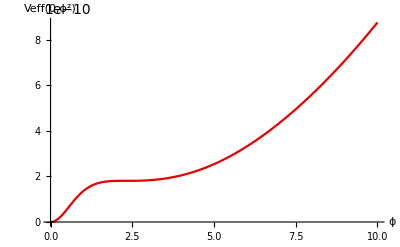

```mathematica
p=0.000000000000001;
GMin=0+p;
GMax=√((48 π)/41)-p;
ψMin=0;
ψMax=100;

V0=0.27/1000000000
F0=428.48/1000

(*F0=0.32*)

Boundarymv[G_]:=V0(((48 π)/41 -G^2)/((48 π)/41));

(*Approximation Original for all values*)
SmoothStep[k_,G_]:=Tanh[k(-(G-Sqrt[(48 π)/41 ]))/(1-(G-Sqrt[(48 π)/41 ])^2)]HeavisideTheta[G-(Sqrt[(48 π)/41 ]-1)]+HeavisideTheta[(Sqrt[(48 π)/41 ]-1)-G];

Boundarymf[G_]:=(41 F0 π)/(41 π-3 F0 Log[(((48 π)/41 -G^2)/((48 π)/41))])SmoothStep[5,G];



eq1=((PerturbedRFP1Func[f,v]/.Derivative[1,0][f][G,0]->0/.Derivative[1,0][v][G,0]->0/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G]))==0);
eq2=((PerturbedRFP2Func[f,v]/.Derivative[1,0][f][G,0]->0/.Derivative[1,0][v][G,0]->0/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G]))==0);

Betag=-((-8192 G^5 π^3 (96 π^2+G^2 (-82 π+3 Derivative[0,1][f][G,0]))-256 G^3 π^2 (-43 G^2+48 π) Derivative[0,1][v][G,0]+3 G (15 G^2-16 π) (Derivative[0,1][v][G,0])^2)/(48 π (128 G^2 π^2+Derivative[0,1][v][G,0])^2));
Betaλ=(-((8192 G^6 π^3 (-36 π+Λ (82 π-3 Derivative[0,1][f][G,0]))+48 π Λ (Derivative[0,1][v][G,0])^2+3 G^2 Derivative[0,1][v][G,0] (4096 π^3 Λ+(-4+15 Λ) Derivative[0,1][v][G,0])+256 G^4 π^2 (3072 π^3 Λ+(-15+43 Λ) Derivative[0,1][v][G,0]))/(24 π (128 G^2 π^2+Derivative[0,1][v][G,0])^2)))16 Pi G+Betag/G λ/.Λ->λ/(16 Pi G)//Simplify;


ReplacedBetag=Betag/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G])//Simplify;
ReplacedBetaλ=Betaλ/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G])//Simplify;

DimlessLambdaNumSol=NDSolve[{((ReplacedBetaλ)/.λ->λ[G])==D[λ[G],G]ReplacedBetag,λ[10^-30]==10^-120},{λ},{G,10^-30,√((48 π)/41)-10^-30},Method->"StiffnessSwitching"];


(*eq1=((G^3(FinalEqvPhiGParityEven/.f^(1,0)[G,0]->0/.v^(1,0)[G,0]->0/.v^(0,1)[G,0]->(0)/.f^(0,1)[G,0]->(0))//Expand)==0);
eq2=((G(FinalEqfPhiGParityEven/.f^(1,0)[G,0]->0/.v^(1,0)[G,0]->0/.v^(0,1)[G,0]->(0)/.f^(0,1)[G,0]->(0))//Expand)==0);
*)


bc1={f[GMax,ψ]==0,v[GMax,ψ]==0};
bc2={f[G,ψMin]==0,v[G,ψMin]==0};

bc3={f[GMin,ϕ]==F0*ψ,v[GMin,ϕ]==V0*ψ^2};

bc4={f[G,ψMax]==Boundaryf[G],v[G,ψMax]==Boundaryv[G]};

bc5={Derivative[0,1][f][G,ψMin]==Boundarymf[G],Derivative[0,1][v][G,ψMin]==Boundarymv[G]};

solvf=NDSolve[{eq1,eq2,Join[bc1,bc2,bc5]},{f,v},{G,GMin,GMax},{ψ,ψMin,ψMax},Method->"Automatic"];

H[x_]:=x*Log[x];

(*Visualize the solution*)
Plot3D[Evaluate[f[G,ψ]/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"g","ϕ",None},PlotLabel->"f(g, ϕ^2)",ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][x]](*,PlotLegends->BarLegend[{{"Rainbow","Reverse"},{0,1}},LabelStyle->Directive[Black,16],"Ticks"->{0,1},"TickLabels"->{"k=0","k=∞"}]*)]

Plot3D[Evaluate[10^8 v[G,ψ]/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"g","ϕ",None},PlotLabel->"10^8v(g, ϕ^2)",ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][x]](*,PlotLegends->BarLegend[{{"Rainbow","Reverse"},{0,1}},LabelStyle->Directive[Black,16],"Ticks"->{0,1},"TickLabels"->{"k=0","k=∞"}]*)]

(*(*Visualize the solution*)
ResourceFunction["CombinePlots"][Plot[Evaluate[f[G,ψ]/. solvf/.G->GMin],{ψ,ψMin,ψMax},PlotRange->All,PlotLegends->{"f(0, ψ)"},PlotStyle->Red,Frame->True],Plot[Evaluate[v[G,ψ]/. solvf/.G->GMin],{ψ,ψMin,ψMax},PlotRange->All,PlotLegends->{"v(0, ψ)"},PlotStyle->Blue,Frame->True,FrameStyle->Blue,AxesLabel->{"ψ"}],"AxesSides"->"TwoY",AxesLabel->{"ψ"}]
*)
Plot3D[Evaluate[((λ[G]/.DimlessLambdaNumSol)+v[G,ψ])/(1+f[G,ψ])^2/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"G","ϕ","Veff(G, ϕ^2)"},ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][x]]]

Plot3D[Evaluate[v[G,ψ]/(1+f[G,ψ])^2/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"G","ϕ","Veff(G, ϕ^2)"},ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][x]]]

Plot3D[Evaluate[(λ[G]/.DimlessLambdaNumSol)/(1+f[G,ψ])^2/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"G","ϕ","Veff(G, ϕ^2)"},ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][x]]]
(*Plot3D[Evaluate[((λ[G]/.DimlessLambdaNumSol)+v[G,ψ])/(1+f[G,ψ])^2/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"G","ϕ","Veff(G, ϕ^2)"},MeshFunctions->{#3&},ScalingFunctions->"Log"]*)

Plot[Evaluate[((0)+v[G,ψ])/(1+f[G,ψ])^2/. solvf/.G->GMin/.ψ->ϕ^2],{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"ϕ","Veff(0,ϕ^2)"},PlotStyle->RGBColor[0.9,0,0]]


(*cuts3dveff=Table[Evaluate[((λ[GMax*(G/GMax)^4]/.DimlessLambdaNumSol)+v[GMax*(G/GMax)^4,ψ])/((1+f[GMax*(G/GMax)^4,ψ])^2)/. solvf/.ψ->ϕ^2],{G,GMin,GMax,GMax/20}];

cuts3dveff=Table[Evaluate[((λ[GMax*(G/GMax)^3]/.DimlessLambdaNumSol)+v[GMax*(G/GMax)^3,ψ])/((1+f[GMax*(G/GMax)^3,ψ])^2)/. solvf/.ψ->ϕ^2],{G,GMin,GMax,GMax/30}];

cf=Blend[{RGBColor[0.9,0,0],RGBColor[0.5,0,1]},#]&;

Plot[cuts3dveff,{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"ϕ","Veff(k,ϕ^2)"},ScalingFunctions->{"Log","Log"},PlotStyle->Table[ColorData["Rainbow",((Length[cuts3dveff]-1)-i)/(Length[cuts3dveff]-1)],{i,0,Length[cuts3dveff]-1}],PlotLegends->BarLegend[{{"Rainbow","Reverse"},{0,1}},LabelStyle->Directive[Black,16],"Ticks"->{0,1},"TickLabels"->{"k=0","k=∞"}]]*)
```

#### Different Boundary Conditions and their results

```mathematica
ListOfSolsf={};
NumerOfValuesf=9;
Listofvaluesf={0.1,0.2,0.3,0.4,42/100,0.5,0.6,0.7,0.8}
For[i=1,i<=Length[Listofvaluesf],i++,

V0=0.275/1000000000;
F0=0.35/0.85;
F0=0.42;

(*V0=0.27/1000000000
F0=428.48/1000*)

V0=0.27/1000000000;
F0=428.48/1000;

F0=Listofvaluesf[[i]];

Boundarymv[G_]:=V0(((48 π)/41 -G^2)/((48 π)/41));

(*Original*)
Boundarymf[G_]:=(41 F0 π)/(41 π-3 F0 Log[(((48 π)/41 -G^2)/((48 π)/41))]);

(*Approximation for values of F0<<1*)
pal=0.1;
Boundarymf[G_]:=(41 F0 π)/(41 π-3 F0 (((((48 π)/41 -G^2)/((48 π)/41))^pal-(((48 π)/41 -G^2)/((48 π)/41))^-pal)/(2 pal)));
(*Approximation for values of F0~1*)
Boundarymf[G_]:=F0(((48 π)/41 -G^2)/((48 π)/41))^(1/1.4);
m=1+(1)/(2 √((3 π)/41));
Boundarymf[G_]:=F0(ⅇ^(1/41 (-1+m) (41 G-4 √(123 π) ArcCoth[(4 √((3 π)/41))/G])));
(*Approximation Original for all values*)
SmoothStep[k_,G_]:=Tanh[k(-(G-Sqrt[(48 π)/41 ]))/(1-(G-Sqrt[(48 π)/41 ])^2)]HeavisideTheta[G-(Sqrt[(48 π)/41 ]-1)]+HeavisideTheta[(Sqrt[(48 π)/41 ]-1)-G];

Boundarymf[G_]:=(41 F0 π)/(41 π-3 F0 Log[(((48 π)/41 -G^2)/((48 π)/41))])SmoothStep[5,G];



eq1=((PerturbedRFP1Func[f,v]/.Derivative[1,0][f][G,0]->0/.Derivative[1,0][v][G,0]->0/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G]))==0);
eq2=((PerturbedRFP2Func[f,v]/.Derivative[1,0][f][G,0]->0/.Derivative[1,0][v][G,0]->0/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G]))==0);


bc1={f[GMax,ψ]==0,v[GMax,ψ]==0};
  bc2={f[G,ψMin]==0,v[G,ψMin]==0};

bc5={Derivative[0,1][f][G,ψMin]==Boundarymf[G],Derivative[0,1][v][G,ψMin]==Boundarymv[G]};

solvf=NDSolve[{eq1,eq2,Join[bc1,bc2,bc5]},{f,v},{G,GMin,GMax},{ψ,ψMin,ψMax},Method->"Automatic"];

AppendTo[ListOfSolsf,solvf[[1]]]

]
```

{0.1,0.2,0.3,0.4,21/50,0.5,0.6,0.7,0.8}

```mathematica
(*Variation of f with different boundary conditions*)
```

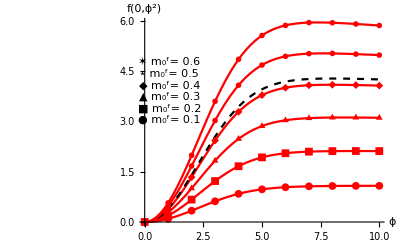

m_0^v= 2.75 10^-10

```mathematica
data1=Table[{ϕ,Evaluate[f[G,ψ]/. ListOfSolsf[[1]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data2=Table[{ϕ,Evaluate[f[G,ψ]/. ListOfSolsf[[2]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data3=Table[{ϕ,Evaluate[f[G,ψ]/. ListOfSolsf[[3]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data4=Table[{ϕ,Evaluate[f[G,ψ]/. ListOfSolsf[[4]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data6=Table[{ϕ,Evaluate[f[G,ψ]/. ListOfSolsf[[6]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data7=Table[{ϕ,Evaluate[f[G,ψ]/. ListOfSolsf[[7]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data8=Table[{ϕ,Evaluate[f[G,ψ]/. ListOfSolsf[[8]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data9=Table[{ϕ,Evaluate[f[G,ψ]/. ListOfSolsf[[9]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];

Show[Table[If[i==5,Plot[Evaluate[f[G,ψ]/. ListOfSolsf[[i]]/. G->0/. ψ->ϕ^2],{ϕ,0,10},PlotRange->All,PlotStyle->{Black,Dashed}],Plot[Evaluate[f[G,ψ]/. ListOfSolsf[[i]]/. G->0/. ψ->ϕ^2],{ϕ,0,10},PlotRange->All,PlotStyle->{Red}]],{i,1,Length[Listofvaluesf]-2}],ListPlot[{data1,data2,data3,data4,data6,data7(*,data8,data9*)},PlotStyle->{Red},PlotMarkers->{{"●",8},{"■",8},{"▲",8},{"◆",8},{"⋆",8},{"✶",8}(*,{"",8},{"",8}*)}],Epilog->{Inset[Framed[Column[{(*Row[{Style["-",Red]," m_0^f= 0.8"}],Row[{Style["-",Red]," m_0^f= 0.7"}],*)Row[{Style["✶",Red]," m_0^f= 0.6"}],Row[{Style["⋆",Red]," m_0^f= 0.5"}],Row[{Style["◆",Red]," m_0^f= 0.4"}],Row[{Style["▲",Red]," m_0^f= 0.3"}],Row[{Style["■",Red]," m_0^f= 0.2"}],Row[{Style["●",Red]," m_0^f= 0.1"}]}],Background->White],Scaled[{0.12,0.65}]]},AxesLabel->{"ϕ","f(0,ϕ^2)"}]
"m_0^v= 2.75 10^-10"
```

```mathematica
ListOfSolsv={};
NumerOfValuesv=9;
Listofvaluesv={0.1/1000000000,0.201/1000000000,0.27/1000000000,0.3/1000000000,0.4/1000000000,0.5/1000000000,0.6/1000000000,0.7/1000000000,0.8/1000000000}
For[i=1,i<=Length[Listofvaluesv],i++,

V0=0.275/1000000000;
F0=0.35/0.85;
F0=0.42;

(*V0=0.27/1000000000
F0=428.48/1000*)

V0=0.27/1000000000;

F0=428.48/1000;

V0=Listofvaluesv[[i]];

Boundarymv[G_]:=V0(((48 π)/41 -G^2)/((48 π)/41));

(*Original*)
Boundarymf[G_]:=(41 F0 π)/(41 π-3 F0 Log[(((48 π)/41 -G^2)/((48 π)/41))]);

(*Approximation for values of F0<<1*)
pal=0.1;
Boundarymf[G_]:=(41 F0 π)/(41 π-3 F0 (((((48 π)/41 -G^2)/((48 π)/41))^pal-(((48 π)/41 -G^2)/((48 π)/41))^-pal)/(2 pal)));
(*Approximation for values of F0~1*)
Boundarymf[G_]:=F0(((48 π)/41 -G^2)/((48 π)/41))^(1/1.4);
m=1+(1)/(2 √((3 π)/41));
Boundarymf[G_]:=F0(ⅇ^(1/41 (-1+m) (41 G-4 √(123 π) ArcCoth[(4 √((3 π)/41))/G])));
(*Approximation Original for all values*)
SmoothStep[k_,G_]:=Tanh[k(-(G-Sqrt[(48 π)/41 ]))/(1-(G-Sqrt[(48 π)/41 ])^2)]HeavisideTheta[G-(Sqrt[(48 π)/41 ]-1)]+HeavisideTheta[(Sqrt[(48 π)/41 ]-1)-G];

Boundarymf[G_]:=(41 F0 π)/(41 π-3 F0 Log[(((48 π)/41 -G^2)/((48 π)/41))])SmoothStep[5,G];



eq1=((PerturbedRFP1Func[f,v]/.Derivative[1,0][f][G,0]->0/.Derivative[1,0][v][G,0]->0/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G]))==0);
eq2=((PerturbedRFP2Func[f,v]/.Derivative[1,0][f][G,0]->0/.Derivative[1,0][v][G,0]->0/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G]))==0);

(*Betag=-((-8192 G^5 π^3 (96 π^2+G^2 (-82 π+3 f^(0,1)[G,0]))-256 G^3 π^2 (-43 G^2+48 π) v^(0,1)[G,0]+3 G (15 G^2-16 π) (v^(0,1)[G,0])^2)/(48 π (128 G^2 π^2+v^(0,1)[G,0])^2));
Betaλ=(-((8192 G^6 π^3 (-36 π+Λ (82 π-3 f^(0,1)[G,0]))+48 π Λ (v^(0,1)[G,0])^2+3 G^2 v^(0,1)[G,0] (4096 π^3 Λ+(-4+15 Λ) v^(0,1)[G,0])+256 G^4 π^2 (3072 π^3 Λ+(-15+43 Λ) v^(0,1)[G,0]))/(24 π (128 G^2 π^2+v^(0,1)[G,0])^2)))16 Pi G+Betag/G λ/.Λ->λ/(16 Pi G)//Simplify;


ReplacedBetag=Betag/.v^(0,1)[G,0]->(Boundarymv[G])/.f^(0,1)[G,0]->(Boundarymf[G])//Simplify;
ReplacedBetaλ=Betaλ/.v^(0,1)[G,0]->(Boundarymv[G])/.f^(0,1)[G,0]->(Boundarymf[G])//Simplify;

DimlessLambdaNumSol=NDSolve[{((ReplacedBetaλ)/.λ->λ[G])==D[λ[G],G]ReplacedBetag,λ[10^-30]==10^-120},{λ},{G,10^-30,√((48 π)/41)-10^-30},Method->"StiffnessSwitching"];*)


(*eq1=((G^3(FinalEqvPhiGParityEven/.f^(1,0)[G,0]->0/.v^(1,0)[G,0]->0/.v^(0,1)[G,0]->(0)/.f^(0,1)[G,0]->(0))//Expand)==0);
eq2=((G(FinalEqfPhiGParityEven/.f^(1,0)[G,0]->0/.v^(1,0)[G,0]->0/.v^(0,1)[G,0]->(0)/.f^(0,1)[G,0]->(0))//Expand)==0);
*)

bc1={f[GMax,ψ]==0,v[GMax,ψ]==0};
  bc2={f[G,ψMin]==0,v[G,ψMin]==0};

bc5={Derivative[0,1][f][G,ψMin]==Boundarymf[G],Derivative[0,1][v][G,ψMin]==Boundarymv[G]};

solvf=NDSolve[{eq1,eq2,Join[bc1,bc2,bc5]},{f,v},{G,GMin,GMax},{ψ,ψMin,ψMax},Method->"Automatic"];

AppendTo[ListOfSolsv,solvf[[1]]]

]
```

{1.×10^-10,2.01×10^-10,2.7×10^-10,3.×10^-10,4.×10^-10,5.×10^-10,6.×10^-10,7.×10^-10,8.×10^-10}

```mathematica
(*Variation of v with different boundary conditions*)
```

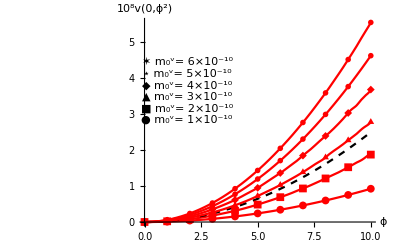

```mathematica
data1v=Table[{ϕ,Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[1]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data2v=Table[{ϕ,Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[2]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data3v=Table[{ϕ,Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[4]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data4v=Table[{ϕ,Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[5]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data6v=Table[{ϕ,Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[6]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data7v=Table[{ϕ,Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[7]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data8v=Table[{ϕ,Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[8]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];
data9v=Table[{ϕ,Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[9]]/. G->0/. ψ->ϕ^2]},{ϕ,0,10,1}];

Show[Table[If[i==3,Plot[Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[i]]/. G->0/. ψ->ϕ^2],{ϕ,0,10},PlotRange->All,PlotStyle->{Black,Dashed}],Plot[Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[i]]/. G->0/. ψ->ϕ^2],{ϕ,0,10},PlotRange->All,PlotStyle->{Red}]],{i,1,Length[Listofvaluesv]-2}],ListPlot[{data1v,data2v,data3v,data4v,data6v,data7v(*,data8,data9*)},PlotStyle->{Red},PlotMarkers->{{"●",8},{"■",8},{"▲",8},{"◆",8},{"⋆",8},{"✶",8}(*,{"",8},{"",8}*)}],Epilog->{Inset[Framed[Column[{(*Row[{Style["-",Red]," m_0^f= 0.8"}],Row[{Style["-",Red]," m_0^f= 0.7"}],*)Row[{Style["✶",Red]," m_0^v= 6×10^-10"}],Row[{Style["⋆",Red]," m_0^v= 5×10^-10"}],Row[{Style["◆",Red]," m_0^v= 4×10^-10"}],Row[{Style["▲",Red]," m_0^v= 3×10^-10"}],Row[{Style["■",Red]," m_0^v= 2×10^-10"}],Row[{Style["●",Red]," m_0^v= 1×10^-10"}]}],Background->White],Scaled[{0.2,0.65}]]},AxesLabel->{"ϕ","10^8v(0,ϕ^2)"}]

(*Show[Table[If[i==3,Plot[Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[i]]/. G->0/. ψ->ϕ^2],{ϕ,0,10},PlotRange->All,PlotStyle->{Black,Dashed}],Plot[Evaluate[10^8 v[G,ψ]/. ListOfSolsv[[i]]/. G->0/. ψ->ϕ^2],{ϕ,0,10},PlotRange->All,PlotStyle->{Red}]],{i,1,Length[Listofvaluesv]}],Epilog->{Inset[Framed[Column[{Row[{Style["-",Red],"m_0^f= 0.1","      m_0^v= 2.75 10^-10"}],Row[{Style["-",Red],"m_0^f= 0.2","      m_0^v= 2.75 10^-10"}],Row[{Style["-",Red],"m_0^f= 0.3","      m_0^v= 2.75 10^-10"}],Row[{Style["-",Red],"m_0^f= 0.4","      m_0^v= 2.75 10^-10"}],Row[{Style["-",Red],"m_0^f= 0.5","      m_0^v= 2.75 10^-10"}],Row[{Style["-",Red],"m_0^f= 0.6","      m_0^v= 2.75 10^-10"}],Row[{Style["-",Red],"m_0^f= 0.7","      m_0^v= 2.75 10^-10"}],Row[{Style["-",Red],"m_0^f= 0.8","      m_0^v= 2.75 10^-10"}]}],Background->White],Scaled[{0.15,0.9}]]},AxesLabel->{"ϕ","v(0,ϕ^2)"}]*)
```

```mathematica
(*Predicted Potentials*)
```

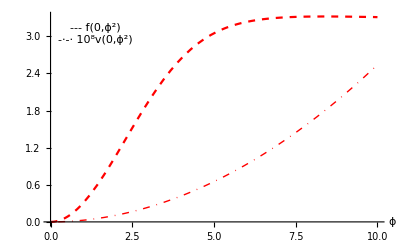

```mathematica
Show[Plot[Evaluate[(10^8 v[G,ψ])/. solvf/. DimlessLambdaNumSol/. G->0/. ψ->ϕ^2],{ϕ,0,10},PlotRange->All,PlotStyle->{Red,DotDashed,Thick}],Plot[Evaluate[f[G,ψ]/. solvf/. DimlessLambdaNumSol/. G->0/. ψ->ϕ^2],{ϕ,0,10},PlotRange->All,PlotStyle->{Red,Dashed}],Epilog->{Inset[Framed[Column[{Row[{Style["---",Red]," f(0,ϕ^2)"}],(*Unicode dash*)Row[{Style["-⋅-⋅",Red]," 10^8v(0,ϕ^2)"}]  (*Unicode dots*)}],Background->White],Scaled[{0.15,0.9}]]},AxesLabel->{"ϕ"," "}]
```

#### Slow Roll Observables of Inflation

```mathematica
(*Define the inflation potential*)
vefftry[ϕ_]:=Evaluate[v[G,ψ]/(1+f[G,ψ])^2/. solvf/.G->GMin/.ψ->ϕ^2][[1]];
(*vefftry[ϕ_]:=(1-Exp[-Sqrt[2/3](Sqrt[8 Pi])ϕ])^2;*)
V[ϕ_]:=vefftry[ϕ];

SquaredDσDPhi[ϕ_]:=1/(1+(f[G,ψ]/. solvf[[1]][[1]]/.G->GMin/.ψ->ϕ^2))+3((D[(1+(f[G,ψ]/. solvf[[1]][[1]]/.G->GMin/.ψ->x^2)),x]/.x->ϕ)^2/(1+(f[G,ψ]/. solvf[[1]][[1]]/.G->GMin/.ψ->ϕ^2))^2);

(*Define the slow-roll parameters*)
ϵ[ϕ_]:=((1/(8Pi))(1/2)(D[V[x],x]/V[x])^2/.x->ϕ)/SquaredDσDPhi[ϕ]//Simplify
η[ϕ_]:=(((1/(8Pi))D[D[V[x],x],x]/V[x]/.x->ϕ)/SquaredDσDPhi[ϕ])-(1/(8Pi))(((D[V[x],x]/V[x])/.x->ϕ)/(SquaredDσDPhi[ϕ])^(3/2))(D[Sqrt[SquaredDσDPhi[x]],x]/.x->ϕ)//Simplify

ns[ϕ_]:=1-6ϵ[ϕ]+2η[ϕ]//Simplify

(*Compute the slow-roll parameters at a specific value of φ*)
slowRollParameters[φ_]:={ϵ[φ],η[φ]}

(*Define the amplitude of scalar fluctuations*)
As[φ_]:=(1/4)(V[φ]/(24 π^2 ϵ[φ]))

(*Define the scalar-to-tensor ratio*)
r[φ_]:=16 ϵ[φ]

(*Define the number of e-folds*)
Nefolds[φ1_,φ2_]:=(Sqrt[8 Pi])NIntegrate[Sqrt[SquaredDσDPhi[ϕ]/(2 ϵ[ϕ])],{ϕ,φ1,φ2}]

(*Example usage:Replace YourValueHere with the desired value of φ*)
valueOfPhi=1.55;
φend=0.25;
(*Calculate slow-roll parameters,amplitude of scalar fluctuations,scalar-to-tensor ratio,and number of e-folds*)
{ϵValue,ηValue,nsValue,AsValue,rValue,NefoldsValue}={ϵ[valueOfPhi],η[valueOfPhi],ns[valueOfPhi],As[valueOfPhi],r[valueOfPhi],Nefolds[φend,valueOfPhi]};
{ϵValue,ηValue,nsValue,AsValue,rValue,NefoldsValue}//N

(*Value of the slow roll observbales at the used end of inflation*)
{ϵ[φend],η[φend]}
```

{0.000433794,-0.0151025,0.967192,4.23188×10^-10,0.0069407,71.5457}

{1.03669,0.767979}

#### Adiabatic evolution of the universe and initial conditions inflaton field

```mathematica
vveeffff[G_,ϕ_]:=(((2*λ[G]/.DimlessLambdaNumSol)+v[G,ψ])/(1+f[G,ψ])^2/. solvf/.ψ->ϕ^2)[[1]][[1]];
```

```mathematica
derivativevveeffff[G_,ϕ_]:=D[vveeffff[G,ϕ],ϕ];
```

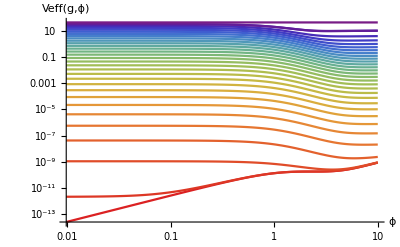

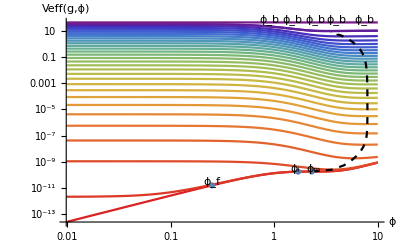

```mathematica
(*cuts3dveff=Table[Evaluate[((λ[GMax*(G/GMax)^4]/.DimlessLambdaNumSol)+v[GMax*(G/GMax)^4,ψ])/((1+f[GMax*(G/GMax)^4,ψ])^2)/. solvf/.ψ->ϕ^2],{G,GMin,GMax,GMax/20}];*)

NSlices=30;
NSlicesEndPart=10;
FPSolvVEFF[ϕ_]:=2*(576/41 √(3/41) π^(3/2));
cuts3dveff=Join[Join[Table[Evaluate[((2*λ[GMax*(G/GMax)^3]/.DimlessLambdaNumSol)+v[GMax*(G/GMax)^3,ψ])/((1+f[GMax*(G/GMax)^3,ψ])^2)/. solvf/.ψ->ϕ^2],{G,GMin,GMax-GMax/NSlices,GMax/NSlices}],Table[Evaluate[((2*λ[GMax*(G/GMax)^3]/.DimlessLambdaNumSol)+v[GMax*(G/GMax)^3,ψ])/((1+f[GMax*(G/GMax)^3,ψ])^2)/. solvf/.ψ->ϕ^2],{G,GMax-GMax/NSlices,GMax-GMax/(NSlices+NSlicesEndPart),GMax/NSlicesEndPart}]],{{{2*(576/41 √(3/41) π^(3/2))}}}];

cf=Blend[{RGBColor[0.9,0,0],RGBColor[0.5,0,1]},#]&;

Plot[cuts3dveff,{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"ϕ","Veff(g,ϕ)"},ScalingFunctions->{"Log","Log"},PlotStyle->Table[ColorData["Rainbow",((Length[cuts3dveff]-1)-i)/(Length[cuts3dveff]-1)],{i,0,Length[cuts3dveff]-1}](*,PlotLegends->BarLegend[{{"Rainbow","Reverse"},{0,1}},LabelStyle->Directive[Black,16],"Ticks"->{0,1},"TickLabels"->{"k=0","k=∞"}]*)]

(*MinimumsPoints=Table[With[{mini=FindRoot[D[cuts3dveff[[i]][[1]][[1]],ϕ]/.ϕ->x,{x,2}][[1]][[2]]},
{mini,(cuts3dveff[[i]][[1]][[1]]/.ϕ->mini)}],{i,1+2,Length[cuts3dveff]-1}];*)
Show[Plot[cuts3dveff,{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"ϕ","Veff(g,ϕ)"},ScalingFunctions->{"Log","Log"},PlotStyle->Table[ColorData["Rainbow",((Length[cuts3dveff]-1)-i)/(Length[cuts3dveff]-1)],{i,0,Length[cuts3dveff]-1}](*,PlotLegends->BarLegend[{{"Rainbow","Reverse"},{0,1}},LabelStyle->Directive[Black,16],"Ticks"->{0,1},"TickLabels"->{"k=0","k=∞"}]*),Epilog->{{Text["ϕ_b",{Log[7.5],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_b",{Log[4],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_b",{Log[2.5],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_b",{Log[0.9],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_b",{Log[1.5],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_f",{Log[φend],Log[V[φend]+0.8*V[φend]]},BaseStyle->{FontSize->8}]},{Text["ϕ_i",{Log[valueOfPhi-0.1],Log[V[valueOfPhi]+0.6*V[valueOfPhi]]},BaseStyle->{FontSize->8}]},{Text["ϕ_m",{Log[2.3+0.1],Log[V[2.3]+0.6*V[2.3]]},BaseStyle->{FontSize->8}]}}(*,Epilog->{{Text["ϕ_b",{10,1},BaseStyle->{FontSize->8}]},{Text["ϕ_f",{φend,V[φend]+0.4*V[φend]},BaseStyle->{FontSize->8}]},{Text["ϕ_i",{valueOfPhi,V[valueOfPhi]+0.05*V[valueOfPhi]},BaseStyle->{FontSize->8}]}}*)](*,ListPlot[Thread[Style[MinimumsPoints,Table[ColorData["Rainbow",((Length[MinimumsPoints]-1)-i)/(Length[MinimumsPoints]-1)],{i,0,Length[MinimumsPoints]-1}]]],ScalingFunctions->{"Log","Log"},PlotMarkers->{Automatic, Tiny}]*),ParametricPlot[With[{ϕ=FindRoot[(D[vveeffff[G,x],x]/.x->y),{y,3}][[1]][[2]]//Re},
{ϕ,(vveeffff[G,ϕ])}],{G,0.000027,1.7},ScalingFunctions->{"Log","Log"},PlotRange->All,AspectRatio->1,PlotStyle->{Black,Dashed}],ListPlot[{{φend,V[φend]},{valueOfPhi,V[valueOfPhi]},{2.3,V[2.3]}},ScalingFunctions->{"Log","Log"},PlotMarkers->{Automatic,Tiny,Black}]]

(*signedLog[x_,α_]:=Sign[x] Log[1+α Abs[x]]/Log[1+α]
Show[Table[ListPlot[Table[{ϕ,Evaluate[Flatten[cuts3dveff][[i+1]]]},{ϕ,Sqrt[ψMin],Sqrt[ψMax],Sqrt[ψMax]/250}],ScalingFunctions->{{signedLog[#,1]&,Exp[α Log[1+#]]-1&},{signedLog[#,1000000000000]&,Exp[α Log[1+#]]-1&}},PlotStyle->ColorData["Rainbow",((Length[cuts3dveff]-1)-i)/(Length[cuts3dveff]-1)],PlotRange->All,AxesOrigin->{0,0}],{i,0,Length[cuts3dveff]-1}],PlotRange->All]*)
```

```mathematica
FindMinimum[(vveeffff[G,x]/.x->y/.G->0.0001),{y,0,10}]
```

{5.99991×10^-12,{y→0.}}

```mathematica
GMax
```

1.9178

```mathematica
grav=90.81;
eqns={x''[t]==-grav D[vveeffff[x[t],y[t]],x[t]],y''[t]==-grav D[vveeffff[x[t],y[t]],y[t]],x[0]==GMax-0.3,y[0]==3.5,x'[0]==0,y'[0]==0};
sol=NDSolve[eqns,{x[t],y[t]},{t,0,10}]
```

InterpolatingFunction::dmval: Input value {-0.0598114,12.5166} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598114} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598114,12.5166} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

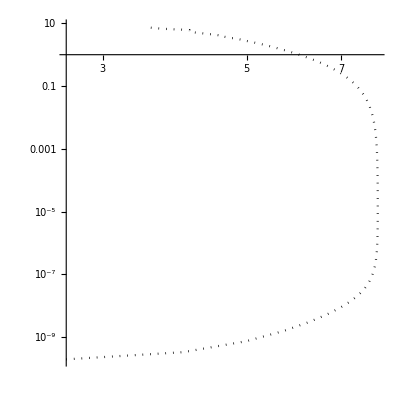

```mathematica
ParametricPlot[With[{ϕ=FindRoot[(D[vveeffff[G,x],x]/.x->y),{y,3}][[1]][[2]]//Re},
{ϕ,(vveeffff[G,ϕ])}],{G,0.0002,1.7},ScalingFunctions->{"Log","Log"},PlotRange->All,AspectRatio->1,PlotStyle->{Black,Dotted}]
```

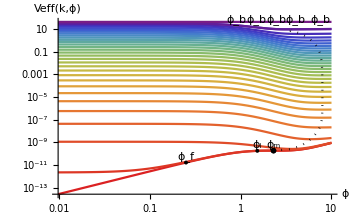

```mathematica
Show[Plot[cuts3dveff,{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"ϕ","Veff(k,ϕ)"},ScalingFunctions->{"Log","Log"},PlotStyle->Table[ColorData["Rainbow",((Length[cuts3dveff]-1)-i)/(Length[cuts3dveff]-1)],{i,0,Length[cuts3dveff]-1}](*,PlotLegends->BarLegend[{{"Rainbow","Reverse"},{0,1}},LabelStyle->Directive[Black,16],"Ticks"->{0,1},"TickLabels"->{"k=0","k=∞"}]*),Epilog->{{Text["ϕ_b",{Log[7.5],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_b",{Log[4],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_b",{Log[2.5],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_b",{Log[0.9],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_b",{Log[1.5],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_f",{Log[φend],Log[V[φend]+2.5*V[φend]]},BaseStyle->{FontSize->8}]},{Text["ϕ_i",{Log[valueOfPhi],Log[V[valueOfPhi]+2*V[valueOfPhi]]},BaseStyle->{FontSize->8}]},{Text["ϕ_m",{Log[2.3],Log[V[2.3]+2*V[2.3]]},BaseStyle->{FontSize->8}]}}(*,Epilog->{{Text["ϕ_b",{10,1},BaseStyle->{FontSize->8}]},{Text["ϕ_f",{φend,V[φend]+0.4*V[φend]},BaseStyle->{FontSize->8}]},{Text["ϕ_i",{valueOfPhi,V[valueOfPhi]+0.05*V[valueOfPhi]},BaseStyle->{FontSize->8}]}}*)](*,ListPlot[Thread[Style[MinimumsPoints,Table[ColorData["Rainbow",((Length[MinimumsPoints]-1)-i)/(Length[MinimumsPoints]-1)],{i,0,Length[MinimumsPoints]-1}]]],ScalingFunctions->{"Log","Log"},PlotMarkers->{Automatic, Tiny}]*),ParametricPlot[With[{ϕ=FindRoot[(D[vveeffff[G,x],x]/.x->y),{y,3}][[1]][[2]]//Re},
{ϕ,(vveeffff[G,ϕ])}],{G,0.000027,1.7},ScalingFunctions->{"Log","Log"},PlotRange->All,AspectRatio->1,PlotStyle->{Black,Dotted}],ListPlot[Thread[Style[{{φend,V[φend]},{valueOfPhi,V[valueOfPhi]}},{Black,Black}]],ScalingFunctions->{"Log","Log"},PlotMarkers->{Automatic,Tiny},PlotStyle->Black],ListPlot[Thread[Style[{{2.3,V[2.3]}},{B}]],ScalingFunctions->{"Log","Log"},PlotMarkers->{"*",Small},PlotStyle->Black]]
```

```mathematica
(*(*Define the inflation potential*)
vefftry[ϕ_]:=Evaluate[v[G,ψ]/(1+f[G,ψ])^2/. solvf/.G->GMin/.ψ->ϕ^2][[1]];
(*vefftry[ϕ_]:=(1-Exp[-Sqrt[2/3](Sqrt[8 Pi])ϕ])^2;*)
V[ϕ_]:=vefftry[ϕ];

FindMinimum[V[ϕ],ϕ]

(*Define the slow-roll parameters*)
ϵ[ϕ_]:=(1/(8Pi))(1/2)(D[V[x],x]/V[x])^2/.x->ϕ
η[ϕ_]:=(1/(8Pi))D[D[V[x],x],x]/V[x]/.x->ϕ

ns[ϕ_]:=1-6ϵ[ϕ]+2η[ϕ]

(*Compute the slow-roll parameters at a specific value of φ*)
slowRollParameters[φ_]:={ϵ[φ],η[φ]}

(*Define the amplitude of scalar fluctuations*)
As[φ_]:=(1/4)(V[φ]/(24 π^2 ϵ[φ]))

(*Define the scalar-to-tensor ratio*)
r[φ_]:=16 ϵ[φ]

(*Define the number of e-folds*)
Nefolds[φ1_,φ2_]:=(Sqrt[8 Pi])NIntegrate[1/(Sqrt[2 ϵ[ϕ]]),{ϕ,φ1,φ2}]

(*Example usage:Replace YourValueHere with the desired value of φ*)
valueOfPhi=1.215;
φend=0.5;
(*Calculate slow-roll parameters,amplitude of scalar fluctuations,scalar-to-tensor ratio,and number of e-folds*)
{ϵValue,ηValue,nsValue,AsValue,rValue,NefoldsValue}={ϵ[valueOfPhi],η[valueOfPhi],ns[valueOfPhi],As[valueOfPhi],r[valueOfPhi],Nefolds[φend,valueOfPhi]};

(*Plot[ϵ[ϕ],{ϕ,1,Sqrt[ψMax]},PlotRange->All,PlotLabel->{"ϵ[ϕ]"},AxesLabel->{"ϕ"}]
Plot[η[ϕ],{ϕ,1,Sqrt[ψMax]},PlotRange->All,PlotLabel->{"η[ϕ]"},AxesLabel->{"ϕ"}]
*)
{ϵValue,ηValue,nsValue,AsValue,rValue,NefoldsValue}//N
{ϵ[φend],η[φend]}
*)
```

#### Numerical relation between both scalar field variables, and inflation in both Einstein and Jordan representations

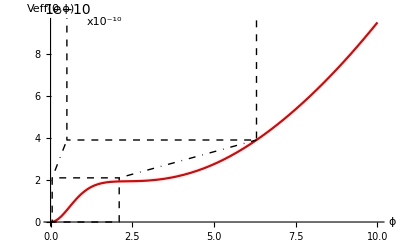

```mathematica
(*Define the zoom-in range*)
zoomRange={{3,4},{0.5,1}};

(*Create the main plot*)
mainPlot=Plot[Evaluate[V[ϕ]],{ϕ,0,10},PlotRange->All,AxesLabel->{"ϕ","Veff(0,ϕ)"},PlotStyle->RGBColor[0.9,0,0]];

(*Create the zoom-in plot*)
zoomPlot=Show[Plot[Evaluate[V[ϕ]],{ϕ,0,2},PlotRange->All,AxesLabel->{"ϕ","x10^-10"},PlotStyle->RGBColor[0.9,0,0],Ticks->{Automatic,Table[{i*10^(-10),i},{i,1,7}]},Epilog->{{Text["ϕ_f",{φend,V[φend]+0.4*V[φend]},BaseStyle->{FontSize->8}]},{Text["ϕ_i",{valueOfPhi,V[valueOfPhi]+0.05*V[valueOfPhi]},BaseStyle->{FontSize->8}]}}],Plot[Evaluate[V[ϕ]],{ϕ,φend,valueOfPhi},PlotRange->{{φend,valueOfPhi},{0,V[valueOfPhi]}},AxesLabel->False,PlotStyle->RGBColor[0.9,0,0],Filling->{1->{Axis,LightGray}}]];

(*Combine the plots using Epilog*)
xrangesqaure1={0.5,6.3};
yrangesqaure1={3.9*10^-10,1*10^-9};
xrangesqaure2={0.05,2.1};
yrangesqaure2={0,2.1*10^-10};

Show[mainPlot,Epilog->{{Dashed,Black,Line[{{xrangesqaure1[[1]],yrangesqaure1[[2]]},{xrangesqaure1[[1]],yrangesqaure1[[1]]},{xrangesqaure1[[2]],yrangesqaure1[[1]]},{xrangesqaure1[[2]],yrangesqaure1[[2]]},{xrangesqaure1[[1]],yrangesqaure1[[2]]}}]},{Dashed,Black,Line[{{xrangesqaure2[[1]],yrangesqaure2[[2]]},{xrangesqaure2[[1]],yrangesqaure2[[1]]},{xrangesqaure2[[2]],yrangesqaure2[[1]]},{xrangesqaure2[[2]],yrangesqaure2[[2]]},{xrangesqaure2[[1]],yrangesqaure2[[2]]}}]},{DotDashed,Black,Line[{{xrangesqaure2[[1]],yrangesqaure2[[2]]},{xrangesqaure1[[1]],yrangesqaure1[[1]]}}]},{DotDashed,Black,Line[{{xrangesqaure2[[2]],yrangesqaure2[[2]]},{xrangesqaure1[[2]],yrangesqaure1[[1]]}}]},Inset[zoomPlot,{3.3,7.3*10^-10},Automatic,Scaled[0.65]],{Text["x10^-10",{1.65,0.95*10^-9},BaseStyle->{FontSize->8}]}},AxesOrigin->{0,0}]
```

```mathematica
φend
valueOfPhi
```

0.25

1.55

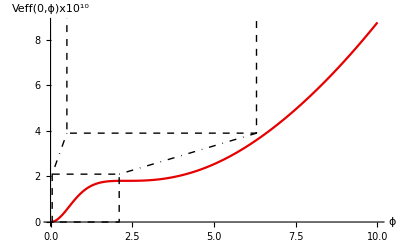

```mathematica
(*Define the zoom-in range*)
zoomRange={{3,4},{0.5,1}};

(*Create the main plot*)
mainPlot=Plot[Evaluate[10^10 V[ϕ]],{ϕ,0,10},PlotRange->All,AxesLabel->{"ϕ","Veff(0,ϕ)x10^10"},PlotStyle->RGBColor[0.9,0,0]];

(*Create the zoom-in plot*)
zoomPlot=Show[Plot[Evaluate[10^10 V[ϕ]],{ϕ,0,2},PlotRange->All,AxesLabel->{"ϕ","x10^-10"},PlotStyle->RGBColor[0.9,0,0],Ticks->{Automatic,Table[{i*10^(-10),i},{i,1,7}]},Epilog->{{Text["ϕ_f",{φend,10^10 V[φend]+0.4*10^10 V[φend]},BaseStyle->{FontSize->8}]},{Text["ϕ_i",{valueOfPhi,10^10 V[valueOfPhi]+0.05*10^10 V[valueOfPhi]},BaseStyle->{FontSize->8}]}}],Plot[Evaluate[10^10 V[ϕ]],{ϕ,φend,valueOfPhi},PlotRange->{{φend,valueOfPhi},{0,10^10 V[valueOfPhi]}},AxesLabel->False,PlotStyle->RGBColor[0.9,0,0],Filling->{1->{Axis,LightGray}}]];

(*Combine the plots using Epilog*)
xrangesqaure1={0.5,6.3};
yrangesqaure1={3.9*10^-10 10^10,0.925*10^-9 10^10};
xrangesqaure2={0.05,2.1};
yrangesqaure2={0,2.1*10^-10 10^10};

Show[mainPlot,Epilog->{{Dashed,Black,Line[{{xrangesqaure1[[1]],yrangesqaure1[[2]]},{xrangesqaure1[[1]],yrangesqaure1[[1]]},{xrangesqaure1[[2]],yrangesqaure1[[1]]},{xrangesqaure1[[2]],yrangesqaure1[[2]]},{xrangesqaure1[[1]],yrangesqaure1[[2]]}}]},{Dashed,Black,Line[{{xrangesqaure2[[1]],yrangesqaure2[[2]]},{xrangesqaure2[[1]],yrangesqaure2[[1]]},{xrangesqaure2[[2]],yrangesqaure2[[1]]},{xrangesqaure2[[2]],yrangesqaure2[[2]]},{xrangesqaure2[[1]],yrangesqaure2[[2]]}}]},{DotDashed,Black,Line[{{xrangesqaure2[[1]],yrangesqaure2[[2]]},{xrangesqaure1[[1]],yrangesqaure1[[1]]}}]},{DotDashed,Black,Line[{{xrangesqaure2[[2]],yrangesqaure2[[2]]},{xrangesqaure1[[2]],yrangesqaure1[[1]]}}]},Inset[zoomPlot,{3.2,7.*10^-10 10^10},Automatic,Scaled[0.65]](*,{Text["x10^-10",{1.65,0.95*10^-9 10^10},BaseStyle->{FontSize->8}]}*)},AxesOrigin->{0,0}]
```

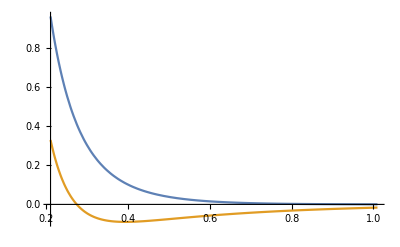

```mathematica
Plot[{ϵ[φ],η[φ]},{φ,φend,valueOfPhi},PlotRange->All]
```

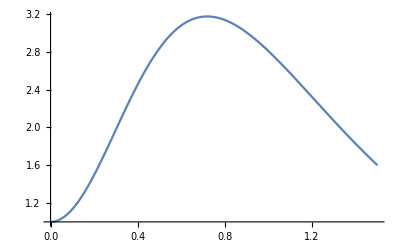

```mathematica
Plot[SquaredDσDPhi[ϕ],{ϕ,Sqrt[ψMin],1.5}]
```

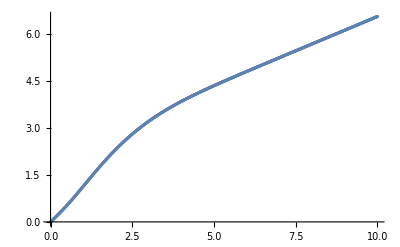

```mathematica
ListPlot[Table[{i,Evaluate[NIntegrate[Sqrt[SquaredDσDPhi[ϕ]],{ϕ,0,i}]]},{i,0,10,10/1000}]]
```

```mathematica
Relationphisigma[σ_]:=Fit[Table[{i,Evaluate[NIntegrate[Sqrt[SquaredDσDPhi[ϕ]],{ϕ,0,i}]]},{i,0,10,10/1000}],Table[σ^i,{i,1,20}],σ]
Relationphisigma[x]
```

1.01443 x-0.276816 x^2+4.40332 x^3-8.33443 x^4+8.35797 x^5-5.50474 x^6+2.55398 x^7-0.85752 x^8+0.209614 x^9-0.036784 x^10+0.00440486 x^11-0.000302576 x^12+3.8557×10^-7 x^13+2.18541×10^-6 x^14-2.01478×10^-7 x^15+4.42983×10^-9 x^16+5.80288×10^-10 x^17-5.5373×10^-11 x^18+2.03062×10^-12 x^19-2.9015×10^-14 x^20

```mathematica
Relationphisigma[x_]:=1.0144320711429446 x-0.2768160850452305 x^2+4.4033188254794675 x^3-8.334432665431494 x^4+8.35797348489644 x^5-5.504735556142244 x^6+2.5539770731934706 x^7-0.8575197700518055 x^8+0.2096137701030596 x^9-0.036784032098504386 x^10+0.0044048577636803705 x^11-0.0003025757671599893 x^12+3.855700039742958*^-7 x^13+2.1854057393505065*^-6 x^14-2.014783992676096*^-7 x^15+4.4298281805213065*^-9 x^16+5.802876075232104*^-10 x^17-5.537297525956771*^-11 x^18+2.030620842922488*^-12 x^19-2.901499231585573*^-14 x^20;
```

```mathematica
Relationphisigma[valueOfPhi]
Relationphisigma[φend]
```

2.33439

0.279514

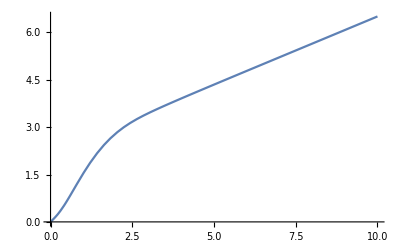

```mathematica
Plot[Relationphisigma[x],{x,0,10}]
```

```mathematica
Relationphisigma[10]
```

6.50284

```mathematica
DataRelationSigmaPhi=Table[{i,Evaluate[InverseFunction[Relationphisigma][x]/.x->i]},{i,0,6.5,6.5/1000}];
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction::ifun will be suppressed during this calculation.

```mathematica
RelationSigmaPhi[σ_]:=Fit[DataRelationSigmaPhi,Table[σ^i,{i,1,20}],σ]
```

```mathematica
RelationSigmaPhi[x]
```

0.89914 x+1.96718 x^2-17.0688 x^3+61.2645 x^4-131.999 x^5+188.562 x^6-187.803 x^7+134.381 x^8-70.2204 x^9+26.8904 x^10-7.44023 x^11+1.41279 x^12-0.152239 x^13-0.00223405 x^14+0.00412883 x^15-0.000797809 x^16+0.0000861025 x^17-5.70144×10^-6 x^18+2.17615×10^-7 x^19-3.69138×10^-9 x^20

```mathematica
RelationSigmaPhi[x_]:=0.8991396865314971 x+1.967181001136907 x^2-17.06879768517796 x^3+61.264529808347284 x^4-131.99912501601892 x^5+188.56162852511494 x^6-187.8028050090628 x^7+134.38081262018187 x^8-70.22036558942087 x^9+26.89036885723407 x^10-7.440231147481368 x^11+1.4127852200643563 x^12-0.15223935923530368 x^13-0.0022340537618645868 x^14+0.004128833178370614 x^15-0.000797808962564419 x^16+0.0000861025496268408 x^17-5.701440158264137*^-6 x^18+2.1761542265691754*^-7 x^19-3.6913786408659463*^-9 x^20;
```

```mathematica
(*This one works badly apparently*)
```

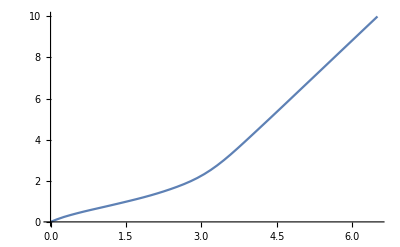

```mathematica
Plot[{Evaluate[Re[RelationSigmaPhi[x]]]},{x,0,6.5}]
```

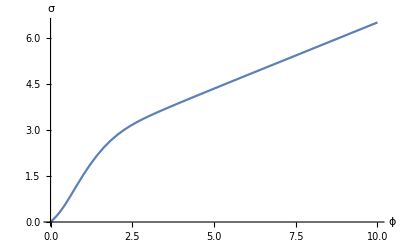

```mathematica
Plot[{Relationphisigma[x]},{x,0,10},AxesLabel->{"ϕ","σ"}]
```

```mathematica
DataV=Table[{i,Evaluate[V[i]]},{i,0,10,10/1000}];
FitV[ψ_]:=Fit[DataV,Table[ψ^i,{i,1,20}],ψ]
```

```mathematica
FitV[ψ]
```

3.94959×10^-12 ψ+2.20135×10^-10 ψ^2+2.7426×10^-10 ψ^3-9.09899×10^-10 ψ^4+9.35919×10^-10 ψ^5-5.3846×10^-10 ψ^6+1.91638×10^-10 ψ^7-3.97932×10^-11 ψ^8+2.34209×10^-12 ψ^9+1.29942×10^-12 ψ^10-4.71866×10^-13 ψ^11+8.09174×10^-14 ψ^12-7.38128×10^-15 ψ^13+9.875×10^-17 ψ^14+6.84284×10^-17 ψ^15-1.0055×10^-17 ψ^16+7.60928×10^-19 ψ^17-3.4457×10^-20 ψ^18+8.88424×10^-22 ψ^19-1.01071×10^-23 ψ^20

```mathematica
FitV[ψ_]:=3.949585097193416*^-12 ψ+2.201351372591046*^-10 ψ^2+2.7425955622831397*^-10 ψ^3-9.09899075577633*^-10 ψ^4+9.359192858917332*^-10 ψ^5-5.384596042775848*^-10 ψ^6+1.91637921993739*^-10 ψ^7-3.979320772114377*^-11 ψ^8+2.34208960134982*^-12 ψ^9+1.2994176639217797*^-12 ψ^10-4.718663285597769*^-13 ψ^11+8.09174445176208*^-14 ψ^12-7.381280067392978*^-15 ψ^13+9.875001125133478*^-17 ψ^14+6.84283935630987*^-17 ψ^15-1.0055041864331423*^-17 ψ^16+7.60928076468835*^-19 ψ^17-3.445697682052084*^-20 ψ^18+8.8842394304558*^-22 ψ^19-1.0107106748891725*^-23 ψ^20;
```

```mathematica
Evaluate[RelationSigmaPhi[x]/.x->σ]
```

0.89914 σ+1.96718 σ^2-17.0688 σ^3+61.2645 σ^4-131.999 σ^5+188.562 σ^6-187.803 σ^7+134.381 σ^8-70.2204 σ^9+26.8904 σ^10-7.44023 σ^11+1.41279 σ^12-0.152239 σ^13-0.00223405 σ^14+0.00412883 σ^15-0.000797809 σ^16+0.0000861025 σ^17-5.70144×10^-6 σ^18+2.17615×10^-7 σ^19-3.69138×10^-9 σ^20

```mathematica
(*This is how the inflaton potential looks in the Jordan frame scalar field σ*)
```

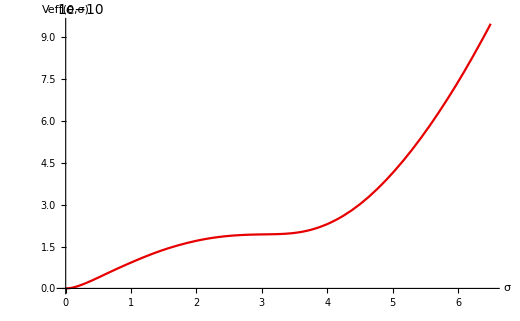

```mathematica
(*Define the main plot range*)


(*Define the zoom-in range*)
zoomRange={{3,4},{0.5,1}};

(*Create the main plot*)
mainPlot=Plot[Evaluate[FitV[Evaluate[RelationSigmaPhi[σ]]]],{σ,0,6.5},PlotRange->All,AxesLabel->{"σ","Veff(0,σ)"},PlotStyle->RGBColor[0.9,0,0]];

(*Create the zoom-in plot*)
zoomPlot=Plot[Evaluate[FitV[Evaluate[RelationSigmaPhi[σ]]]],{σ,0,3},PlotRange->All,AxesLabel->{"σ","Veff(0,σ)"},PlotStyle->RGBColor[0.9,0,0]];

(*Combine the plots using Epilog*)
Show[mainPlot,Epilog->Inset[zoomPlot,{2.23,6*10^-10},Automatic,Scaled[0.65]]]
```

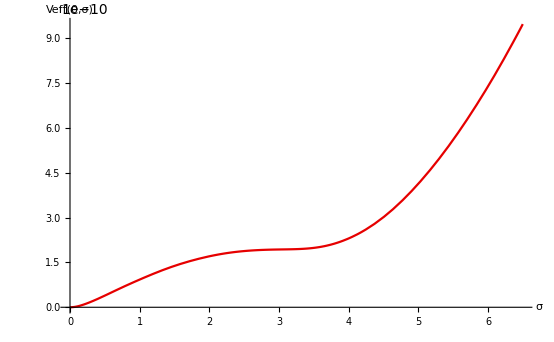

```mathematica
Plot[Evaluate[FitV[Evaluate[RelationSigmaPhi[σ]]]],{σ,0,6.5},PlotRange->All,AxesLabel->{"σ","Veff(0,σ)"},PlotStyle->RGBColor[0.9,0,0]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

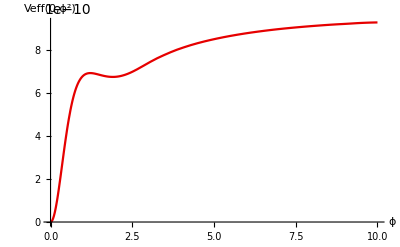

```mathematica
PerturbedRFP1Func[f_,v_]:=1/(256 G^5 π^2)((256 G^7 π (-((4 π (1+f[G,ψ])+3 ψ (Derivative[0,1][f][G,ψ])^2) Derivative[0,1][v][G,0])+4 π (1+f[G,ψ]) (Derivative[0,1][v][G,ψ]+2 ψ Derivative[0,2][v][G,ψ])))/((128 G^2 π^2+Derivative[0,1][v][G,0]) (32 G^2 π (4 π (1+f[G,ψ])+3 ψ (Derivative[0,1][f][G,ψ])^2)+(1+f[G,ψ]) (Derivative[0,1][v][G,ψ]+2 ψ Derivative[0,2][v][G,ψ])))+((24576 G^7 π^3 Derivative[0,1][f][G,0]-G (128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0])) (2 v[G,ψ]-ψ Derivative[0,1][v][G,ψ]))/(12 π (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0]))+G (4 v[G,ψ]-2 ψ Derivative[0,1][v][G,ψ]+(G (-24576 G^6 π^3 Derivative[0,1][f][G,0]+(128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0])) Derivative[1,0][v][G,ψ])/(24 π (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0]))));
PerturbedRFP2Func[f_,v_]:=-1/(384 π^2)(37-(48 π (1+f[G,ψ]))/G^2+(48 π ψ Derivative[0,1][f][G,ψ])/G^2+(8 (1+f[G,ψ]) (256 G^4 π^2 (4 π (1+f[G,ψ])+3 ψ (Derivative[0,1][f][G,ψ])^2) (8 π-3 Derivative[0,1][f][G,ψ]-6 ψ Derivative[0,2][f][G,ψ])+48 G^2 π (4 π (1+f[G,ψ])+3 ψ (Derivative[0,1][f][G,ψ])^2) (Derivative[0,1][v][G,ψ]+2 ψ Derivative[0,2][v][G,ψ])+(1+f[G,ψ]) (Derivative[0,1][v][G,ψ]+2 ψ Derivative[0,2][v][G,ψ])^2))/(32 G^2 π (4 π (1+f[G,ψ])+3 ψ (Derivative[0,1][f][G,ψ])^2)+(1+f[G,ψ]) (Derivative[0,1][v][G,ψ]+2 ψ Derivative[0,2][v][G,ψ]))^2+(2 ψ Derivative[0,1][f][G,ψ] (24576 G^6 π^3 Derivative[0,1][f][G,0]-(128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0])))/(G^2 (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0]))+(2 f[G,ψ] (-24576 G^6 π^3 Derivative[0,1][f][G,0]+(128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0])))/(G^2 (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0]))+(-49152 G^6 π^3 Derivative[0,1][f][G,0]+2 (128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0]))/(G^2 (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0]))+((24576 G^6 π^3 Derivative[0,1][f][G,0]-(128 G^2 π^2+Derivative[0,1][v][G,0]) (128 G^2 (41 G^2-48 π) π^2+(45 G^2-48 π) Derivative[0,1][v][G,0])) Derivative[1,0][f][G,ψ])/(G (128 G^2 π^2+Derivative[0,1][v][G,0])^2 (-2+G Derivative[1,0][f][G,0])));

p=0.0000000000001;
GMin=0+p;
GMax=√((48 π)/41)-p;
ψMin=0;
ψMax=100;



V0=0.275/100;
F0=0;


V0=0.275/100000000;
F0=0.95/0.85;


m=0;
n=3+2(1);
Boundarymf[G_]:=F0(4^(m-1)  (16-(41 G^2)/(3 π))^(1/2 (1-m)));
Boundarymv[G_]:=V0(4^(3-n) (16-(41 G^2)/(3 π))^(1/2 (-3+n)));


eq1=((PerturbedRFP1Func[f,v]/.Derivative[1,0][f][G,0]->0/.Derivative[1,0][v][G,0]->0/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G]))==0);
eq2=((PerturbedRFP2Func[f,v]/.Derivative[1,0][f][G,0]->0/.Derivative[1,0][v][G,0]->0/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G]))==0);


Betag=-((-8192 G^5 π^3 (96 π^2+G^2 (-82 π+3 Derivative[0,1][f][G,0]))-256 G^3 π^2 (-43 G^2+48 π) Derivative[0,1][v][G,0]+3 G (15 G^2-16 π) (Derivative[0,1][v][G,0])^2)/(48 π (128 G^2 π^2+Derivative[0,1][v][G,0])^2));
Betaλ=(-((8192 G^6 π^3 (-36 π+Λ (82 π-3 Derivative[0,1][f][G,0]))+48 π Λ (Derivative[0,1][v][G,0])^2+3 G^2 Derivative[0,1][v][G,0] (4096 π^3 Λ+(-4+15 Λ) Derivative[0,1][v][G,0])+256 G^4 π^2 (3072 π^3 Λ+(-15+43 Λ) Derivative[0,1][v][G,0]))/(24 π (128 G^2 π^2+Derivative[0,1][v][G,0])^2)))16 Pi G+Betag/G λ/.Λ->λ/(16 Pi G)//Simplify;


ReplacedBetag=Betag/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G])//Simplify;
ReplacedBetaλ=Betaλ/.Derivative[0,1][v][G,0]->(Boundarymv[G])/.Derivative[0,1][f][G,0]->(Boundarymf[G])//Simplify;

DimlessLambdaNumSol=NDSolve[{((ReplacedBetaλ)/.λ->λ[G])==D[λ[G],G]ReplacedBetag,λ[10^-30]==10^-120},{λ},{G,10^-15,√((48 π)/41)-10^-15},Method->"StiffnessSwitching"];


(*eq1=((G^3(FinalEqvPhiGParityEven/.f^(1,0)[G,0]->0/.v^(1,0)[G,0]->0/.v^(0,1)[G,0]->(0)/.f^(0,1)[G,0]->(0))//Expand)==0);
eq2=((G(FinalEqfPhiGParityEven/.f^(1,0)[G,0]->0/.v^(1,0)[G,0]->0/.v^(0,1)[G,0]->(0)/.f^(0,1)[G,0]->(0))//Expand)==0);
*)


bc1={f[GMax,ψ]==0,v[GMax,ψ]==0};
bc2={f[G,ψMin]==0,v[G,ψMin]==0};

bc3={f[GMin,ϕ]==F0*ψ,v[GMin,ϕ]==V0*ψ^2};

bc4={f[G,ψMax]==Boundaryf[G],v[G,ψMax]==Boundaryv[G]};

bc5={Derivative[0,1][f][G,ψMin]==Boundarymf[G],Derivative[0,1][v][G,ψMin]==Boundarymv[G]};

solvf=NDSolve[{eq1,eq2,Join[bc1,bc2,bc5]},{f,v},{G,GMin,GMax},{ψ,ψMin,ψMax},Method->"Automatic"];


(*Visualize the solution*)
Plot3D[Evaluate[f[G,ψ]/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"g","ϕ","f(g, ϕ^2)"},ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][x]]]

Plot3D[Evaluate[v[G,ψ]/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"g","ϕ","v(g, ϕ^2)"},ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][x]]]

(*(*Visualize the solution*)
ResourceFunction["CombinePlots"][Plot[Evaluate[f[G,ψ]/. solvf/.G->GMin],{ψ,ψMin,ψMax},PlotRange->All,PlotLegends->{"f(0, ψ)"},PlotStyle->Red,Frame->True],Plot[Evaluate[v[G,ψ]/. solvf/.G->GMin],{ψ,ψMin,ψMax},PlotRange->All,PlotLegends->{"v(0, ψ)"},PlotStyle->Blue,Frame->True,FrameStyle->Blue,AxesLabel->{"ψ"}],"AxesSides"->"TwoY",AxesLabel->{"ψ"}]
*)
Plot3D[Evaluate[((2*λ[G]/.DimlessLambdaNumSol)+v[G,ψ])/(1+f[G,ψ])^2/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"G","ϕ","Veff(G, ϕ^2)"},ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][x]]]

Plot3D[Evaluate[v[G,ψ]/(1+f[G,ψ])^2/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"g","ϕ","Veff(g, ϕ^2)"},ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][x]]]

Plot3D[Evaluate[(2*λ[G]/.DimlessLambdaNumSol)/(1+f[G,ψ])^2/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"G","ϕ","Veff(G, ϕ^2)"},ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][x]]]
(*Plot3D[Evaluate[((λ[G]/.DimlessLambdaNumSol)+v[G,ψ])/(1+f[G,ψ])^2/. solvf/.ψ->ϕ^2],{G,GMin,GMax},{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"G","ϕ","Veff(G, ϕ^2)"},MeshFunctions->{#3&},ScalingFunctions->"Log"]*)

Plot[Evaluate[((0)+v[G,ψ])/(1+f[G,ψ])^2/. solvf/.G->GMin/.ψ->ϕ^2],{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"ϕ","Veff(0,ϕ^2)"},PlotStyle->RGBColor[0.9,0,0]]
```

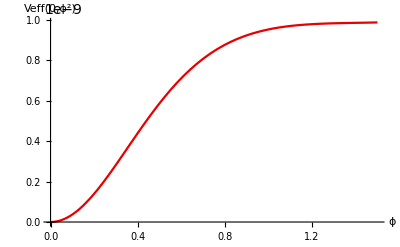

```mathematica
Plot[Evaluate[v[G,ψ]/(1+f[G,ψ])^2/. solvf/.G->GMin/.ψ->  ϕ^2],{ϕ,Sqrt[ψMin],1.5},PlotRange->All,AxesLabel->{"ϕ","Veff(0,ϕ^2)"},PlotStyle->RGBColor[0.9,0,0]]
(*Plot[Evaluate[D[v[G,ψ]/(1+f[G,ψ])^2/. solvf/.G->GMin/.ψ->  ϕ^2,ϕ]],{ϕ,Sqrt[ψMin],1.5},PlotRange->All,AxesLabel->{"ϕ","Veff(0,ϕ^2)"},PlotStyle->RGBColor[0.9,0,0]]*)
```

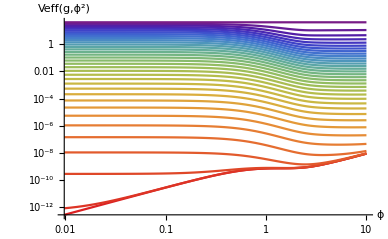

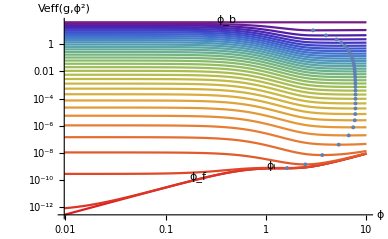

```mathematica
(*cuts3dveff=Table[Evaluate[((λ[GMax*(G/GMax)^4]/.DimlessLambdaNumSol)+v[GMax*(G/GMax)^4,ψ])/((1+f[GMax*(G/GMax)^4,ψ])^2)/. solvf/.ψ->ϕ^2],{G,GMin,GMax,GMax/20}];*)

NSlices=35;
NSlicesEndPart=10;
FPSolvVEFF[ϕ_]:=2*(576/41 √(3/41) π^(3/2));
cuts3dveff=Join[Join[Table[Evaluate[((2*λ[GMax*(G/GMax)^3]/.DimlessLambdaNumSol)+v[GMax*(G/GMax)^3,ψ])/((1+f[GMax*(G/GMax)^3,ψ])^2)/. solvf/.ψ->ϕ^2],{G,GMin,GMax-GMax/NSlices,GMax/NSlices}],Table[Evaluate[((2*λ[GMax*(G/GMax)^3]/.DimlessLambdaNumSol)+v[GMax*(G/GMax)^3,ψ])/((1+f[GMax*(G/GMax)^3,ψ])^2)/. solvf/.ψ->ϕ^2],{G,GMax-GMax/NSlices,GMax-GMax/(NSlices+NSlicesEndPart),GMax/NSlicesEndPart}]],{{{2*(576/41 √(3/41) π^(3/2))}}}];

cf=Blend[{RGBColor[0.9,0,0],RGBColor[0.5,0,1]},#]&;

Plot[cuts3dveff,{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"ϕ","Veff(g,ϕ^2)"},ScalingFunctions->{"Log","Log"},PlotStyle->Table[ColorData["Rainbow",((Length[cuts3dveff]-1)-i)/(Length[cuts3dveff]-1)],{i,0,Length[cuts3dveff]-1}](*,PlotLegends->BarLegend[{{"Rainbow","Reverse"},{0,1}},LabelStyle->Directive[Black,16],"Ticks"->{0,1},"TickLabels"->{"k=0","k=∞"}]*)]

MinimumsPoints=Table[With[{mini=FindRoot[D[cuts3dveff[[i]][[1]][[1]],ϕ]/.ϕ->x,{x,3}][[1]][[2]]},
{mini,(cuts3dveff[[i]][[1]][[1]]/.ϕ->mini)}],{i,1+2,Length[cuts3dveff]-1}];
Show[Plot[cuts3dveff,{ϕ,Sqrt[ψMin],Sqrt[ψMax]},PlotRange->All,AxesLabel->{"ϕ","Veff(g,ϕ^2)"},ScalingFunctions->{"Log","Log"},PlotStyle->Table[ColorData["Rainbow",((Length[cuts3dveff]-1)-i)/(Length[cuts3dveff]-1)],{i,0,Length[cuts3dveff]-1}](*,PlotLegends->BarLegend[{{"Rainbow","Reverse"},{0,1}},LabelStyle->Directive[Black,16],"Ticks"->{0,1},"TickLabels"->{"k=0","k=∞"}]*),Epilog->{{Text["ϕ_b",{Log[0.4],Log[2*(576/41 √(3/41) π^(3/2))+30]},BaseStyle->{FontSize->8}]},{Text["ϕ_f",{Log[φend],Log[V[φend]+0.6*V[φend]]},BaseStyle->{FontSize->8}]},{Text["ϕ_i",{Log[valueOfPhi+0.1],Log[V[valueOfPhi]+0.6*V[valueOfPhi]]},BaseStyle->{FontSize->8}]}}(*,Epilog->{{Text["ϕ_b",{10,1},BaseStyle->{FontSize->8}]},{Text["ϕ_f",{φend,V[φend]+0.4*V[φend]},BaseStyle->{FontSize->8}]},{Text["ϕ_i",{valueOfPhi,V[valueOfPhi]+0.05*V[valueOfPhi]},BaseStyle->{FontSize->8}]}}*)],ListPlot[Thread[Style[MinimumsPoints,Table[ColorData["Rainbow",((Length[MinimumsPoints]-1)-i)/(Length[MinimumsPoints]-1)],{i,0,Length[MinimumsPoints]-1}]]],ScalingFunctions->{"Log","Log"},PlotMarkers->{Automatic, Tiny}]]

(*signedLog[x_,α_]:=Sign[x] Log[1+α Abs[x]]/Log[1+α]
Show[Table[ListPlot[Table[{ϕ,Evaluate[Flatten[cuts3dveff][[i+1]]]},{ϕ,Sqrt[ψMin],Sqrt[ψMax],Sqrt[ψMax]/250}],ScalingFunctions->{{signedLog[#,1]&,Exp[α Log[1+#]]-1&},{signedLog[#,1000000000000]&,Exp[α Log[1+#]]-1&}},PlotStyle->ColorData["Rainbow",((Length[cuts3dveff]-1)-i)/(Length[cuts3dveff]-1)],PlotRange->All,AxesOrigin->{0,0}],{i,0,Length[cuts3dveff]-1}],PlotRange->All]*)
```

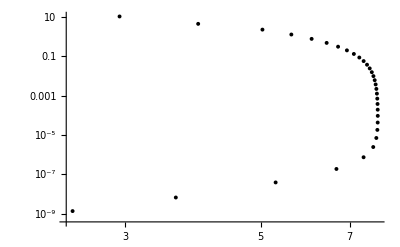

```mathematica
ListPlot[MinimumsPoints,ScalingFunctions->{"Log","Log"},PlotMarkers->{Automatic, Tiny},PlotStyle->Black]
```

```mathematica
With[{mini=FindMinimum[{cuts3dveff[[10]][[1]][[1]],1<ϕ<10},ϕ][[2]][[1]][[2]]},
{mini,(cuts3dveff[[3]][[1]][[1]]/.ϕ->mini)}]
```

{5.09166,2.41396×10^-9}

```mathematica
(((2*λ[G]/.DimlessLambdaNumSol)+v[G,ψ])/(1+f[G,ψ])^2/. solvf/.ψ->ϕ^2)[[1]][[1]]
```

(2 InterpolatingFunction[…][G]+InterpolatingFunction[…][G,ϕ^2])/((1+InterpolatingFunction[…][G,ϕ^2])^2)

```mathematica
vveeffff[G_,ϕ_]:=(2 InterpolatingFunction[…][G]+InterpolatingFunction[…][G,ϕ^2])/((1+InterpolatingFunction[…][G,ϕ^2])^2);
```

```mathematica
D[(2 InterpolatingFunction[…][G]+InterpolatingFunction[…][G,ϕ^2])/((1+InterpolatingFunction[…][G,ϕ^2])^2),ϕ]
```

(2 ϕ InterpolatingFunction[…][G,ϕ^2])/((1+InterpolatingFunction[…][G,ϕ^2])^2)-(4 ϕ (2 InterpolatingFunction[…][G]+InterpolatingFunction[…][G,ϕ^2]) InterpolatingFunction[…][G,ϕ^2])/(1+InterpolatingFunction[…][G,ϕ^2])^3

```mathematica
derivativevveeffff[G_,ϕ_]:=(2 ϕ InterpolatingFunction[…][G,ϕ^2])/((1+InterpolatingFunction[…][G,ϕ^2])^2)-(4 ϕ (2 InterpolatingFunction[…][G]+InterpolatingFunction[…][G,ϕ^2]) InterpolatingFunction[…][G,ϕ^2])/(1+InterpolatingFunction[…][G,ϕ^2])^3;
```

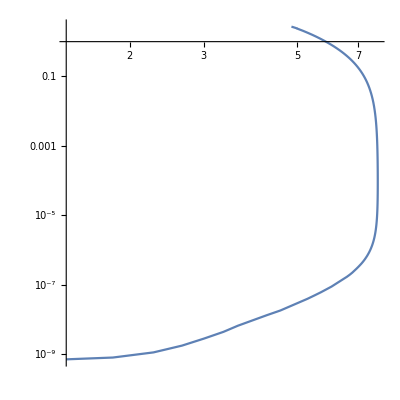

```mathematica
ParametricPlot[With[{ϕ=FindRoot[Evaluate[derivativevveeffff[G,x]],{x,1,0.01,10}][[1]][[2]]},
{ϕ,(vveeffff[G,ϕ])}],{G,0.00008,1.5},ScalingFunctions->{"Log","Log"},PlotRange->All,AspectRatio->1]
```

```mathematica
Exp[2*(576/41 √(3/41) π^(3/2))]//N
```

2.39905×10^18

```mathematica
Exp[]
```

```mathematica
(*(*Define the inflation potential*)
vefftry[ϕ_]:=Evaluate[v[G,ψ]/(1+f[G,ψ])^2/. solvf/.G->GMin/.ψ->ϕ^2][[1]];
(*vefftry[ϕ_]:=(1-Exp[-Sqrt[2/3](Sqrt[8 Pi])ϕ])^2;*)
V[ϕ_]:=vefftry[ϕ];

FindMinimum[V[ϕ],ϕ]

(*Define the slow-roll parameters*)
ϵ[ϕ_]:=(1/(8Pi))(1/2)(D[V[x],x]/V[x])^2/.x->ϕ
η[ϕ_]:=(1/(8Pi))D[D[V[x],x],x]/V[x]/.x->ϕ

ns[ϕ_]:=1-6ϵ[ϕ]+2η[ϕ]

(*Compute the slow-roll parameters at a specific value of φ*)
slowRollParameters[φ_]:={ϵ[φ],η[φ]}

(*Define the amplitude of scalar fluctuations*)
As[φ_]:=(1/4)(V[φ]/(24 π^2 ϵ[φ]))

(*Define the scalar-to-tensor ratio*)
r[φ_]:=16 ϵ[φ]

(*Define the number of e-folds*)
Nefolds[φ1_,φ2_]:=(Sqrt[8 Pi])NIntegrate[1/(Sqrt[2 ϵ[ϕ]]),{ϕ,φ1,φ2}]

(*Example usage:Replace YourValueHere with the desired value of φ*)
valueOfPhi=1.215;
φend=0.5;
(*Calculate slow-roll parameters,amplitude of scalar fluctuations,scalar-to-tensor ratio,and number of e-folds*)
{ϵValue,ηValue,nsValue,AsValue,rValue,NefoldsValue}={ϵ[valueOfPhi],η[valueOfPhi],ns[valueOfPhi],As[valueOfPhi],r[valueOfPhi],Nefolds[φend,valueOfPhi]};

(*Plot[ϵ[ϕ],{ϕ,1,Sqrt[ψMax]},PlotRange->All,PlotLabel->{"ϵ[ϕ]"},AxesLabel->{"ϕ"}]
Plot[η[ϕ],{ϕ,1,Sqrt[ψMax]},PlotRange->All,PlotLabel->{"η[ϕ]"},AxesLabel->{"ϕ"}]
*)
{ϵValue,ηValue,nsValue,AsValue,rValue,NefoldsValue}//N
{ϵ[φend],η[φend]}
*)
```

```mathematica
(*Define the inflation potential*)
vefftry[ϕ_]:=Evaluate[v[G,ψ]/(1+f[G,ψ])^2/. solvf/.G->GMin/.ψ->ϕ^2][[1]];
(*vefftry[ϕ_]:=(1-Exp[-Sqrt[2/3](Sqrt[8 Pi])ϕ])^2;*)
V[ϕ_]:=vefftry[ϕ];

SquaredDσDPhi[ϕ_]:=1/(1+(f[G,ψ]/. solvf[[1]][[1]]/.G->GMin/.ψ->ϕ^2))+3((D[(1+(f[G,ψ]/. solvf[[1]][[1]]/.G->GMin/.ψ->x^2)),x]/.x->ϕ)^2/(1+(f[G,ψ]/. solvf[[1]][[1]]/.G->GMin/.ψ->ϕ^2))^2);

(*Define the slow-roll parameters*)
ϵ[ϕ_]:=((1/(8Pi))(1/2)(D[V[x],x]/V[x])^2/.x->ϕ)/SquaredDσDPhi[ϕ]//Simplify
η[ϕ_]:=(((1/(8Pi))D[D[V[x],x],x]/V[x]/.x->ϕ)/SquaredDσDPhi[ϕ])-(1/(8Pi))(((D[V[x],x]/V[x])/.x->ϕ)/(SquaredDσDPhi[ϕ])^(3/2))(D[Sqrt[SquaredDσDPhi[x]],x]/.x->ϕ)//Simplify

ns[ϕ_]:=1-6ϵ[ϕ]+2η[ϕ]//Simplify

(*Compute the slow-roll parameters at a specific value of φ*)
slowRollParameters[φ_]:={ϵ[φ],η[φ]}

(*Define the amplitude of scalar fluctuations*)
As[φ_]:=(1/4)(V[φ]/(24 π^2 ϵ[φ]))

(*Define the scalar-to-tensor ratio*)
r[φ_]:=16 ϵ[φ]

(*Define the number of e-folds*)
Nefolds[φ1_,φ2_]:=(Sqrt[8 Pi])NIntegrate[Sqrt[SquaredDσDPhi[ϕ]/(2 ϵ[ϕ])],{ϕ,φ1,φ2}]

(*Example usage:Replace YourValueHere with the desired value of φ*)
valueOfPhi=1.01;
φend=0.21;
(*Calculate slow-roll parameters,amplitude of scalar fluctuations,scalar-to-tensor ratio,and number of e-folds*)
{ϵValue,ηValue,nsValue,AsValue,rValue,NefoldsValue}={ϵ[valueOfPhi],η[valueOfPhi],ns[valueOfPhi],As[valueOfPhi],r[valueOfPhi],Nefolds[φend,valueOfPhi]};
{ϵValue,ηValue,nsValue,AsValue,rValue,NefoldsValue}//N
{ϵ[φend],η[φend]}
```

{0.000353979,-0.0163169,0.965242,2.06184×10^-9,0.00566367,66.3911}

{0.96302,0.330065}

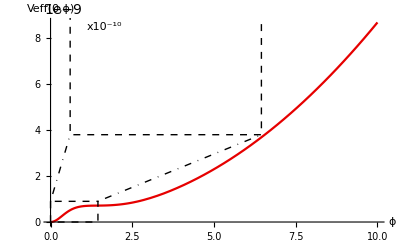

```mathematica
(*Define the zoom-in range*)
zoomRange={{3,4},{0.5,1}};

(*Create the main plot*)
mainPlot=Plot[Evaluate[V[ϕ]],{ϕ,0,10},PlotRange->All,AxesLabel->{"ϕ","Veff(0,ϕ)"},PlotStyle->RGBColor[0.9,0,0]];

(*Create the zoom-in plot*)
zoomPlot=Show[Plot[Evaluate[V[ϕ]],{ϕ,0,1.5},PlotRange->All,AxesLabel->{"ϕ","x10^-10"},PlotStyle->RGBColor[0.9,0,0],Ticks->{Automatic,Table[{i*10^(-10),i},{i,1,7}]},Epilog->{{Text["ϕ_f",{φend,V[φend]+0.4*V[φend]},BaseStyle->{FontSize->8}]},{Text["ϕ_i",{valueOfPhi,V[valueOfPhi]+0.05*V[valueOfPhi]},BaseStyle->{FontSize->8}]}}],Plot[Evaluate[V[ϕ]],{ϕ,φend,valueOfPhi},PlotRange->{{φend,valueOfPhi},{0,V[valueOfPhi]}},AxesLabel->False,PlotStyle->RGBColor[0.9,0,0],Filling->{1->{Axis,LightGray}}]];

(*Combine the plots using Epilog*)
xrangesqaure1={0.6,6.45};
yrangesqaure1={3.8*10^-9,9.1*10^-9};
xrangesqaure2={0,1.45};
yrangesqaure2={0,9*10^-10};

Show[mainPlot,Epilog->{{Dashed,Black,Line[{{xrangesqaure1[[1]],yrangesqaure1[[2]]},{xrangesqaure1[[1]],yrangesqaure1[[1]]},{xrangesqaure1[[2]],yrangesqaure1[[1]]},{xrangesqaure1[[2]],yrangesqaure1[[2]]},{xrangesqaure1[[1]],yrangesqaure1[[2]]}}]},{Dashed,Black,Line[{{xrangesqaure2[[1]],yrangesqaure2[[2]]},{xrangesqaure2[[1]],yrangesqaure2[[1]]},{xrangesqaure2[[2]],yrangesqaure2[[1]]},{xrangesqaure2[[2]],yrangesqaure2[[2]]},{xrangesqaure2[[1]],yrangesqaure2[[2]]}}]},{DotDashed,Black,Line[{{xrangesqaure2[[1]],yrangesqaure2[[2]]},{xrangesqaure1[[1]],yrangesqaure1[[1]]}}]},{DotDashed,Black,Line[{{xrangesqaure2[[2]],yrangesqaure2[[2]]},{xrangesqaure1[[2]],yrangesqaure1[[1]]}}]},Inset[zoomPlot,{3.4,6.9*10^-9},Automatic,Scaled[0.65]],{Text["x10^-10",{1.65,8.5*10^-9},BaseStyle->{FontSize->8}]}},AxesOrigin->{0,0}]
```

```mathematica
Plot[{ϵ[φ],η[φ]},{φ,φend,valueOfPhi},PlotRange->All]
```

-Graphics-

```mathematica
Plot[SquaredDσDPhi[ϕ],{ϕ,Sqrt[ψMin],1.5}]
```

-Graphics-

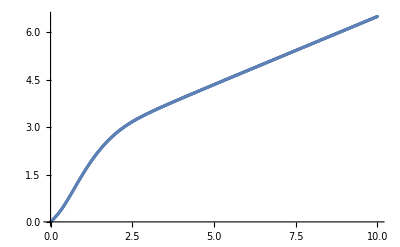

```mathematica
ListPlot[Table[{i,Evaluate[NIntegrate[Sqrt[SquaredDσDPhi[ϕ]],{ϕ,0,i}]]},{i,0,10,10/1000}]]
```

```mathematica
Relationphisigma[σ_]:=Fit[Table[{i,Evaluate[NIntegrate[Sqrt[SquaredDσDPhi[ϕ]],{ϕ,0,i}]]},{i,0,10,10/1000}],Table[σ^i,{i,1,20}],σ]
Relationphisigma[x]
```

1.01443 x-0.276816 x^2+4.40332 x^3-8.33443 x^4+8.35797 x^5-5.50474 x^6+2.55398 x^7-0.85752 x^8+0.209614 x^9-0.036784 x^10+0.00440486 x^11-0.000302576 x^12+3.8557×10^-7 x^13+2.18541×10^-6 x^14-2.01478×10^-7 x^15+4.42983×10^-9 x^16+5.80288×10^-10 x^17-5.5373×10^-11 x^18+2.03062×10^-12 x^19-2.9015×10^-14 x^20

```mathematica
Relationphisigma[x_]:=1.0144320711429446 x-0.2768160850452305 x^2+4.4033188254794675 x^3-8.334432665431494 x^4+8.35797348489644 x^5-5.504735556142244 x^6+2.5539770731934706 x^7-0.8575197700518055 x^8+0.2096137701030596 x^9-0.036784032098504386 x^10+0.0044048577636803705 x^11-0.0003025757671599893 x^12+3.855700039742958*^-7 x^13+2.1854057393505065*^-6 x^14-2.014783992676096*^-7 x^15+4.4298281805213065*^-9 x^16+5.802876075232104*^-10 x^17-5.537297525956771*^-11 x^18+2.030620842922488*^-12 x^19-2.901499231585573*^-14 x^20;
```

```mathematica
Relationphisigma[valueOfPhi]
Relationphisigma[φend]
```

1.54986

0.228378

```mathematica
Plot[Relationphisigma[x],{x,0,10}]
```

-Graphics-

```mathematica
Relationphisigma[10]
```

6.50284

```mathematica
DataRelationSigmaPhi=Table[{i,Evaluate[InverseFunction[Relationphisigma][x]/.x->i]},{i,0,6.5,6.5/1000}];
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction::ifun will be suppressed during this calculation.

```mathematica
RelationSigmaPhi[σ_]:=Fit[DataRelationSigmaPhi,Table[σ^i,{i,1,20}],σ]
```

```mathematica
RelationSigmaPhi[x]
```

0.89914 x+1.96718 x^2-17.0688 x^3+61.2645 x^4-131.999 x^5+188.562 x^6-187.803 x^7+134.381 x^8-70.2204 x^9+26.8904 x^10-7.44023 x^11+1.41279 x^12-0.152239 x^13-0.00223405 x^14+0.00412883 x^15-0.000797809 x^16+0.0000861025 x^17-5.70144×10^-6 x^18+2.17615×10^-7 x^19-3.69138×10^-9 x^20

```mathematica
RelationSigmaPhi[x_]:=0.8991396865314971 x+1.967181001136907 x^2-17.06879768517796 x^3+61.264529808347284 x^4-131.99912501601892 x^5+188.56162852511494 x^6-187.8028050090628 x^7+134.38081262018187 x^8-70.22036558942087 x^9+26.89036885723407 x^10-7.440231147481368 x^11+1.4127852200643563 x^12-0.15223935923530368 x^13-0.0022340537618645868 x^14+0.004128833178370614 x^15-0.000797808962564419 x^16+0.0000861025496268408 x^17-5.701440158264137*^-6 x^18+2.1761542265691754*^-7 x^19-3.6913786408659463*^-9 x^20;
```

```mathematica
(*This one works badly apparently*)
```

```mathematica
Plot[{Evaluate[Re[RelationSigmaPhi[x]]]},{x,0,6.5}]
```

-Graphics-

```mathematica
Plot[{Relationphisigma[x]},{x,0,10}]
```

-Graphics-

```mathematica
DataV=Table[{i,Evaluate[V[i]]},{i,0,10,10/1000}];
FitV[ψ_]:=Fit[DataV,Table[ψ^i,{i,1,20}],ψ]
```

```mathematica
FitV[ψ]
```

-6.2731×10^-11 ψ+3.36712×10^-9 ψ^2-1.19822×10^-9 ψ^3-1.03412×10^-8 ψ^4+2.08253×10^-8 ψ^5-2.08405×10^-8 ψ^6+1.33966×10^-8 ψ^7-6.02063×10^-9 ψ^8+1.96228×10^-9 ψ^9-4.69394×10^-10 ψ^10+8.15231×10^-11 ψ^11-9.76805×10^-12 ψ^12+6.64142×10^-13 ψ^13+7.93737×10^-15 ψ^14-7.7704×10^-15 ψ^15+9.68654×10^-16 ψ^16-6.81749×10^-17 ψ^17+2.96245×10^-18 ψ^18-7.45646×10^-20 ψ^19+8.37521×10^-22 ψ^20

```mathematica
FitV[ψ_]:=-6.27310384399249*^-11 ψ+3.3671195028839376*^-9 ψ^2-1.1982206312246412*^-9 ψ^3-1.0341240521317216*^-8 ψ^4+2.082533984127326*^-8 ψ^5-2.084050701351592*^-8 ψ^6+1.3396562370891301*^-8 ψ^7-6.020625423673613*^-9 ψ^8+1.962284240530368*^-9 ψ^9-4.69393877573618*^-10 ψ^10+8.152307241952249*^-11 ψ^11-9.768045452121972*^-12 ψ^12+6.641415764939967*^-13 ψ^13+7.937366043332502*^-15 ψ^14-7.770403855588582*^-15 ψ^15+9.686544417472832*^-16 ψ^16-6.817492668630379*^-17 ψ^17+2.9624451720118215*^-18 ψ^18-7.456455956858736*^-20 ψ^19+8.37520814385069*^-22 ψ^20;
```

```mathematica
Evaluate[RelationSigmaPhi[x]/.x->σ]
```

0.89914 σ+1.96718 σ^2-17.0688 σ^3+61.2645 σ^4-131.999 σ^5+188.562 σ^6-187.803 σ^7+134.381 σ^8-70.2204 σ^9+26.8904 σ^10-7.44023 σ^11+1.41279 σ^12-0.152239 σ^13-0.00223405 σ^14+0.00412883 σ^15-0.000797809 σ^16+0.0000861025 σ^17-5.70144×10^-6 σ^18+2.17615×10^-7 σ^19-3.69138×10^-9 σ^20

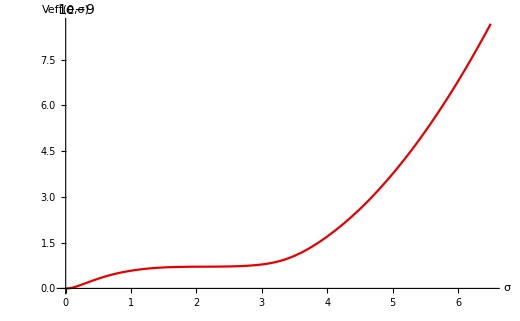

```mathematica
(*Define the main plot range*)


(*Define the zoom-in range*)
zoomRange={{3,4},{0.5,1}};

(*Create the main plot*)
mainPlot=Plot[Evaluate[FitV[Evaluate[RelationSigmaPhi[σ]]]],{σ,0,6.5},PlotRange->All,AxesLabel->{"σ","Veff(0,σ)"},PlotStyle->RGBColor[0.9,0,0]];

(*Create the zoom-in plot*)
zoomPlot=Plot[Evaluate[FitV[Evaluate[RelationSigmaPhi[σ]]]],{σ,0,2.3},PlotRange->All,AxesLabel->{"σ","Veff(0,σ)"},PlotStyle->RGBColor[0.9,0,0]];

(*Combine the plots using Epilog*)
Show[mainPlot,Epilog->Inset[zoomPlot,{2.4,6*10^-9},Automatic,Scaled[0.65]]]
```

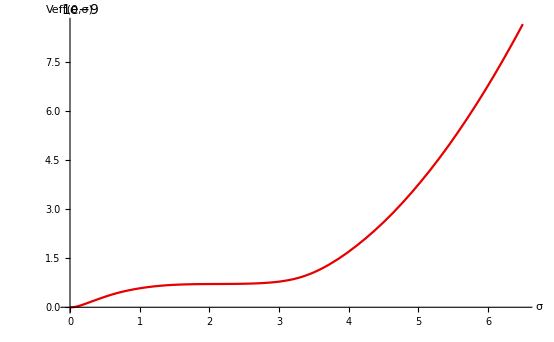

```mathematica
Plot[Evaluate[FitV[Evaluate[RelationSigmaPhi[σ]]]],{σ,0,6.5},PlotRange->All,AxesLabel->{"σ","Veff(0,σ)"},PlotStyle->RGBColor[0.9,0,0]]
```

```mathematica
Plot[Evaluate[FitV[(0.7295162143052571 x-0.3465746169601289 x^2+1.461508616691442 x^3-4.7990551832003 x^4+8.759171513302007 x^5-9.857893768401581 x^6+7.3631794531573656 x^7-3.796863022048575 x^8+1.3738355739728219 x^9-0.3465952800440799 x^10+0.0583441682114664 x^11-0.005585122001424609 x^12+0.00004442300480086652 x^13+0.00006218564399455904 x^14-6.9515294279980415*^-6 x^15+2.5485458185911122*^-8 x^16+6.180889001471609*^-8 x^17-6.287219494643622*^-9 x^18+2.792331613605603*^-10 x^19-4.942202854142527*^-12 x^20/.x->σ//N)]],{σ,0,7.1},PlotRange->All,AxesLabel->{"σ","Veff(0,σ)"},PlotStyle->RGBColor[0.9,0,0]]
```

General::ivar: 0.729516 σ-0.346575 σ^2+1.46151 σ^3-4.79906 σ^4+8.75917 σ^5-9.85789 σ^6+7.36318 σ^7-3.79686 σ^8+1.37384 σ^9-0.346595 σ^10+«10» is not a valid variable.

General::ivar: 0.000105804 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

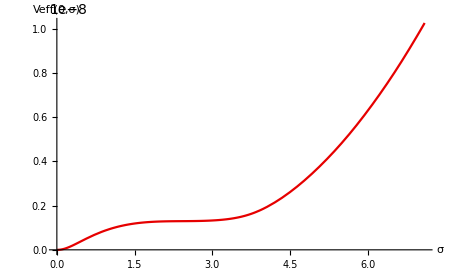

```mathematica
Plot[Evaluate[FitV[RelationSigmaPhiInverse[σ]]],{σ,0,7.1},PlotRange->All,AxesLabel->{"σ","Veff(0,σ)"},PlotStyle->RGBColor[0.9,0,0]]
```

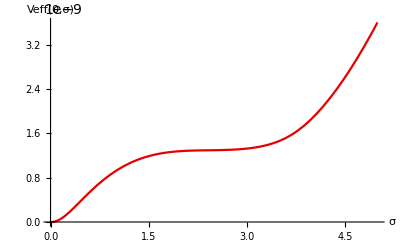

```mathematica
Plot[Evaluate[FitV[RelationSigmaPhiInverse[σ]]],{σ,0,5},PlotRange->All,AxesLabel->{"σ","Veff(0,σ)"},PlotStyle->RGBColor[0.9,0,0]]
```